# Mutual inductance between rectangular circuits

This  notebook is part of the supplemental material for the paper An inductive field component of the electric field that corresponds to Faraday’s law. The enclosed source code is used to find numerical solutions of electromagnetic force (EMF) due to mutual inductance between two rectangular wire circuits. This is done for the circuits in both a coplanar and co-axial arrangement, the calculations being performed for a set of horizontal  and vertical separations, respectively. Results are found using Faraday’s law, the full electric field acceleration term, the static field term, and the dynamic field term.

The calculations are done in a set of Mathematica modules in this notebook. The output of the calculations are two tables in the section Comparison of generated EMFs. If your the goal is simply to evaluate different circuit geometries and separations, this can be achieved by modifying parameters in that section and evaluating the notebook.

Note that in two cases the symbols used here differ from the paper. The circuit height is given by h in the paper and by script l here. The vertical separation is v in the paper and is h here.

## Symbol definitions

The layout of the circuits and the symbol definitions are shown below. The driven circuit has a changing current applied to it while the induced voltage is calculated for the measured circuit. As noted above, in the paper the height of the circuit is h and here it is l. Also the vertical separation for the co-axial case is v in the paper and is h here.

-Graphics-

## Equations for EMF using Faraday’s law

The change electromagnetic flux through a point in space due to a current flowing in a wire of length dl is

The total EMF will be the sum of all of individual EMF’s generated by each straight wire segment of the driven circuit on the measured circuit.

where the dimensions are from the circuit diagram above. This is the integral over the area of the measured circuit for all points along the driven wire. The distance between a point on a drive wire segment and a point within the measured circuit is

The current vector parallel to the point on the driven wire.

## Theory and equations for inductive field

For equations using the acceleration terms the EMF is the sum of the forces from one segment of driven wire on a segment of the measured wire. For the dynamic acceleration term

For the standard derivation the acceleration term is replaced by the double cross product term.

The value of the vector r is found from

## Modules overview

The numerical solutions were arrived at using a set of Mathematica modules, each one responsible for either part of the calculation or combining the results. They are arranged rather like classes in object oriented languages.

The most likely use of this notebook is to replicate the results of the paper for the same or different geometries. This is most easily done by copying the section Comparison of generated EMFs and modifying geometries and separations.

Aside from inspecting the source code, a deeper understanding of the modules can come from browsing the unit tests, their input, and their output.

## Comparison of generated EMFs

The table below shows the numerical results of the EMF generated using Faraday’s law, the full acceleration term, the static term, and the dynamic term. The EMF for the Faraday and dynamic acceleration terms are equal or differ in the last few least significant digits.  The full acceleration term is consistently close to zero, and the static term is the negative of the Faraday and dynamic terms.

If you wish to try other geometries, you can copy this section and change the arguments in the call to ComparisonOfEmfForRectangularCircuits, or just do so below and then reevaluate the notebook.

```mathematica
comparisionNear = ComparisonOfEmfForRectangularCircuits[
{0.005, 0.010, 0.025,  0.05, 0.075, 0.1},(* The list of separations, in meters, for co-planar and co-axial separations *)
{0.1, 0.1}, (* The width and length(height in the paper) of the driven circuit, in meters *)
{0.05,0.04}, (* The width and length(height in the paper) of the measured circuit, in meters *)
Automatic
];
```

```mathematica
comparisionNear["writeResultsToTable"][]
```

|  |         Coplanar (μV) |  |  |  |  |        Coaxial (μV) |  |  | 
separation (mm) |  | Faraday | Full accel | Static accel | Dynamic accel |     | Faraday | Full accel | Static accel | Dynamic accel
5. |     | 12.5657 | -0.000049967 | -12.5657 | 12.5657 |     | -24.4164 | 5.08175×10^-7 | 24.4164 | -24.4164
10. |     | 8.09668 | -1.79483×10^-7 | -8.09663 | 8.09663 |     | -23.152 | 4.14725×10^-7 | 23.152 | -23.152
25. |     | 3.52078 | -5.56233×10^-8 | -3.52078 | 3.52078 |     | -17.0874 | 1.35166×10^-6 | 17.0874 | -17.0874
50. |     | 1.43025 | -3.55023×10^-8 | -1.43025 | 1.43025 |     | -8.6877 | 5.63091×10^-8 | 8.6877 | -8.6877
75. |     | 0.742114 | 1.13269×10^-8 | -0.742114 | 0.742114 |     | -4.47633 | -4.54098×10^-9 | 4.47633 | -4.47633
100. |     | 0.439113 | -3.62991×10^-9 | -0.439113 | 0.439113 |     | -2.47621 | -4.04461×10^-10 | 2.47621 | -2.47621

Induced EMF for circuit separation

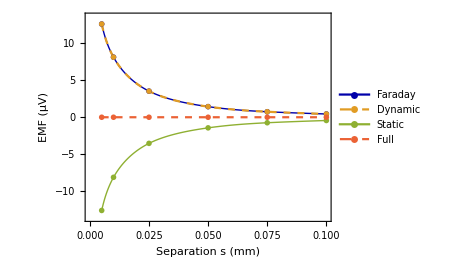

```mathematica
comparisonGraphics =GraphicsForComparisonOfEmfForRectangularCircuits[comparisionNear];
comparisonGraphics["plotEmfsVsSeparation"][]
```

An interesting aspect of the conventional acceleration term is that the sum of EMF’s around a loop of wire is always zero, within numerical accuracy. This is true whether it is a driven wire loop on a single measured wire, or a single driven wire on a measured wire loop. In either case the sum of EMF is zero. The i index refers to the driven and j to the measured wires. The wire with index 1 is on the right and increases counter-clockwise.

```mathematica
comparisionNear["writeWireToWireEmfsToTable"][0.005]
```

Full accel term EMF's (μV) |  |  |  |  |  |  |         Static term EMF's (μV) |  |  |  |  |  |  |         Dynamic term EMF's (μV) |  |  |  |  | 
 | i=1 | 2 | 3 | 4 | Sum |     |  | i=1 | 2 | 3 | 4 | Sum |     |  | i=1 | 2 | 3 | 4 | Sum
j=1 | -5.2745 | 1.4176 | 2.4394 | 1.4176 | 0 |  | j=1 | 1.186 | 1.4176 | -0.0923 | 1.4176 | 3.9288 |  | j=1 | -6.4605 | 0 | 2.5317 | 0 | -3.9288
2 | -1.3392 | -1.6439 | 0.4796 | 2.5035 | 0 |  | 2 | -1.3392 | 4.9808 | 0.4796 | -2.3167 | 1.8045 |  | 2 | 0 | -6.6246 | 0 | 4.8202 | -1.8045
3 | 7.9529 | -2.2772 | -3.3985 | -2.2772 | -0.0001 |  | 3 | -15.8122 | -2.2772 | 0.2632 | -2.2772 | -20.1034 |  | 3 | 23.7651 | 0 | -3.6617 | 0 | 20.1034
4 | -1.3392 | 2.5035 | 0.4796 | -1.6439 | 0 |  | 4 | -1.3392 | -2.3167 | 0.4796 | 4.9808 | 1.8045 |  | 4 | 0 | 4.8202 | 0 | -6.6246 | -1.8045
Sum | 0 | 0 | 0 | 0 | 0 |  |  | -17.3046 | 1.8045 | 1.13 | 1.8045 | -12.5657 |  |  | 17.3046 | -1.8045 | -1.13 | -1.8045 | 12.5657

## Precision and convergence of values

It is shown above that the The table below shows the numerical results of the EMF generated using Faraday’s law, the full acceleration term, the static term, and the dynamic term. The EMF for the Faraday and dynamic acceleration terms are equal or differ in the last few least significant digits.  The full acceleration term is consistently close to zero, and the static term is the negative of the Faraday and dynamic terms.

If you wish to try other geometries, you can copy this section and change the arguments in the call to ComparisonOfEmfForRectangularCircuits, or just do so below and then reevaluate the notebook.

```mathematica
precisionAnalysis = AnalysisOfPrecisionForRectangularCircuits[
0.010,(* Separation *)
{0.1, 0.1}, (* The width and length(height in the paper) of the driven circuit, in meters *)
{0.05,0.04}, (* The width and length(height in the paper) of the measured circuit, in meters *)
 {3, 6, 9, 12,15} (* The precision values *)
];
```

```mathematica
graphics =GraphicsForPrecisionForRectangularCircuits[precisionAnalysis];
```

Difference of Faraday to dynamic acceleration equation for requested precision

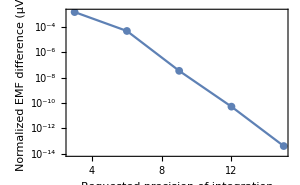

```mathematica
graphics["plotAbsFaradayDiffDynamic"][]
```

Difference of full Feynman acceleration EMF to zero for requested precision

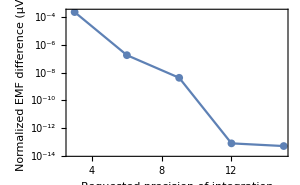

```mathematica
graphics["plotAbsFullDiffZero"][]
```

```mathematica
precisionAnalysis["writeResultsToTable"][]
```

precision |  | Faraday | Difference between Faraday and dynamic accel |  | Full accel | Difference of full accel from zero
3 |     | 8.09835 | 1.55×10^-3 |     | -0.000230 | 2.3×10^-4
6 |     | 8.09668 | 5.01×10^-5 |     | -0.000000 | 1.79×10^-7
9 |     | 8.09663 | 3.56×10^-8 |     | 0.000000 | 4.2×10^-9
12 |     | 8.09663 | 5.29×10^-11 |     | 0.000000 | 7.88×10^-14
15 |     | 8.09663 | 4.09×10^-14 |     | 0.000000 | 5.04×10^-14

## Common functionality

This is the common base ‘class’ for the Faraday and inductive field modules. It mostly has a helper function for the constructing geometry of the circuits.

```mathematica
BaseObject[] := Module[
{
(* public variables *)
this = <||>,

(* public functions *)
wiresFromDimensions,wiresFromCorners,log,makePublic,

(* internal variables *)
 wireList,addCorner,diCorner, subs,argList, iCorner,
},

wiresFromDimensions[circuitDimensions_, offset_ : {0,0,0}] := (
wiresFromCorners[
{
{circuitDimensions[[1]]/2,-circuitDimensions[[2]]/2,0.0}, {circuitDimensions[[1]]/2,circuitDimensions[[2]]/2,0.0},{-circuitDimensions[[1]]/2,circuitDimensions[[2]]/2,0.0},{-circuitDimensions[[1]]/2,-circuitDimensions[[2]]/2,0.0}
},
offset,
True]
);
 
wiresFromCorners[
wireCorners_:{_?NumericQ..}, 
offsetCornersBy_:{_?NumericQ..}, 
isClosed_?BooleanQ
] := (
wireList = {};
addCorner[start_, end_] := AppendTo[wireList,
 <| "start"-> wireCorners[[start]]+offsetCornersBy,
 "end"->  wireCorners[[end]]+offsetCornersBy,
 "wireId"-> start|>];
For[iCorner=1, iCorner< Length[wireCorners], ++iCorner,
addCorner[iCorner, iCorner+1];
];
If[isClosed, addCorner[iCorner, 1]];
wireList
);

	(* Assign a value to this. The argument is a list of the form
		{ string, value, string value,...}
	*)
	makePublic[thisArg_, stringList_] := (
		subs = Partition[stringList, 2];
		argList = thisArg;
		Scan[(argList = AssociateTo[argList, #[[1]]-> #[[2]]])&, subs];
		argList
	);

	log[name_, value_] := Print[name <> ": " <> TextString[value]];
	this = makePublic[this, {
"wiresFromDimensions",wiresFromDimensions,
"wiresFromCorners",wiresFromCorners,
"log", log,
"makePublic", makePublic}];
	this
];
```

## EMF from Faraday’s law

This module calculates the induced EMF from Faraday’s law.

```mathematica
FaradayEmfForRectangularCircuits[precision_] := Module[
{
(* public values *)
this = <||>,

(* constants *)
e0, c,mu0,

(* public functions *)
faradaysEmfWireToWireSet,faradaysEmfWireSetToWireSet,faradayEmfForWireOnWireSetsAtOffsets,wiresFromCorners,

(* local values *)
drivenWireSet,measuredWireSetAtOffset, wireEmf,wireList, iCorner,addCorner,faradayEmfTotal, faradayEmfData, faradayEmfFromWires,srcWireStartFdy,srcWireVecFdy,srcWireLengthFdy,srcWireNormalizedFdy,dIdtVecFdy,msrXWireStartFdy,msrXWireEndFdy,msrYWireStartFdy,msrYWireEndFdy,msrXWireVecFdy,msrXWireLengthFdy,msrXWireNormalizedFdy,msrYWireVecFdy,msrYWireLengthFdy,msrYWireNormalizedFdy,srcWirePosFdy,msrCircuitPosFdy,msrXYDotFdy,log
},
this = BaseObject[];
log = this["log"];

(* Constants *)
e0 = 8.8541878128*^-12;
c = 299792458;
mu0 = 1/(e0 c^2);(* 1.2566370621219*^-6 *)

(* Calculate the EMF from Faraday's law for one driven wire on the measured wire loop. *)
faradaysEmfWireToWireSet[
dIdt_,
srcWire_,
msrWireSet_
] := (
srcWireStartFdy =srcWire["start"];
srcWireVecFdy = srcWire["end"]-srcWire["start"];
srcWireLengthFdy = Norm[srcWireVecFdy];
srcWireNormalizedFdy = Normalize[srcWireVecFdy];
dIdtVecFdy = dIdt srcWireNormalizedFdy;

(* This algorithm assumes that the the measured wire set is a closed
rectangle. The first two sides are used as perpendicular vectors. Start
by verifying this.  *)
msrXWireStartFdy =  msrWireSet[[1]]["start"];
msrXWireEndFdy =  msrWireSet[[1]]["end"];
msrYWireStartFdy =  msrWireSet[[2]]["start"];
msrYWireEndFdy =  msrWireSet[[2]]["end"];

msrXWireVecFdy = msrXWireEndFdy-msrXWireStartFdy;
msrXWireLengthFdy = Norm[msrXWireVecFdy];
msrXWireNormalizedFdy = Normalize[msrXWireVecFdy];

msrYWireVecFdy = msrYWireEndFdy-msrYWireStartFdy;
msrYWireLengthFdy = Norm[msrYWireVecFdy];
msrYWireNormalizedFdy = Normalize[msrYWireVecFdy];

msrXYDotFdy = Dot[msrXWireVecFdy, msrYWireVecFdy]/msrXWireLengthFdy;
If[Abs[msrXYDotFdy] > 0.0001, Throw["Error in faradaysEmfWireToWireSet: Wires not perpendicular"]];

-mu0 /(4*Pi)
NIntegrate[
srcWirePosFdy = srcWireStartFdy+srcWireLinearPosFdy srcWireNormalizedFdy;
msrCircuitPosFdy = msrXWireStartFdy+xmFdy msrXWireNormalizedFdy+ymFdy msrYWireNormalizedFdy;
Dot[
Cross[dIdtVecFdy, msrCircuitPosFdy-srcWirePosFdy],
{0,0,1}
]/Norm[msrCircuitPosFdy-srcWirePosFdy]^3,
 {srcWireLinearPosFdy, 0,srcWireLengthFdy},
{xmFdy, 0,  msrXWireLengthFdy},
{ymFdy, 0, msrYWireLengthFdy},
Method->"LocalAdaptive",
PrecisionGoal->precision
]
);

(* Calculate the EMF from Faraday's law for the driven wire loop on the measured wire loop. *)
faradaysEmfWireSetToWireSet[
dIdt_,
srcWireSet_,
msrWireSet_
] := (
If[srcWireSet // Length ≠ 4, Throw["Error in faradaysEmfWireSetToWireSet: srcWireSet size incorrect, expected 4 but found "<> TextString[srcWireSet //Length]]];

faradayEmfTotal = 0.0;
faradayEmfData=Map[
Function[
{drivenWire},
faradayEmfFromWires = faradaysEmfWireToWireSet[dIdt, drivenWire, msrWireSet];
faradayEmfTotal += faradayEmfFromWires;
<|"drivenWireId"->drivenWire["wireId"], "emfs"-> faradayEmfFromWires|>
],
srcWireSet
];

<| "emfTotal"-> faradayEmfTotal, "drivenWireEmfs"->faradayEmfData|>
);

(* Calculate the EMF from Faraday's law for the driven on measured wire loops for a set of horizontal loop separations. *)
faradayEmfForWireOnWireSetsAtOffsets[
dIdt_?NumericQ,
drivenWireCorners_,
measuredWireCorners_,
measuredXOffsets_
]
:= (
drivenWireSet = this["wiresFromCorners"][drivenWireCorners, {0,0,0}, True];
Map[
Function[
{xOffset},
measuredWireSetAtOffset = this["wiresFromCorners"][
measuredWireCorners,
{xOffset, 0,0},
True];

wireEmf = faradaysEmfWireSetToWireSet[
dIdt,
drivenWireSet, 
measuredWireSetAtOffset
];
{xOffset, wireEmf["emfTotal"]}
],
 measuredXOffsets]
);

this = this["makePublic"][this, {
"faradaysEmfWireToWireSet", faradaysEmfWireToWireSet,
"faradaysEmfWireSetToWireSet", faradaysEmfWireSetToWireSet,
"faradayEmfForWireOnWireSetsAtOffsets", faradayEmfForWireOnWireSetsAtOffsets
}];
this
]
```

## EMF from inductive field

This module calculates the induced EMF from the full, static, and dynamic acceleration terms.

```mathematica
InductiveFieldEmfForRectangularCircuits[precision_] := Module[
{
(* public values *)
this = <||>,

(* constants *)
e0, c,mu0,

(* public variables *)
fullAccelTermCoeff,staticAccelTermCoeff,dynamicAccelTermCoeff,

(* public functions *)
setFullAccelTermCoeff, setStaticAccelTermCoeff,setDynamicAccelTermCoeff,accelProduct, emfAtPoint,emfFromWireToWire,inlineEmfForWires,inlineEmfForWireSetsOnWire,inlineEmfForWireOnWireSets,inlineEmfForWireSetsOnWireSets,inlineEmfForWireOnWireSetsAtOffsets,

(* local values *)
rMsrDrv,drvLen,zeroVec,mDrv,msrLen,mMsr,dIdtVec,rrVec, drvWireVec, drvWireLength,drvWireNormalized, drvWirePos, msrWireLength, msrWireNormalized, msrWirePos, msrWireVec, emfResult,xyEmf, emfVec, inlineEmf,emfTotal,drivenWireEmfs,wireEmf, measuredWireEmfs, emfTotalForSets, drivenWireSet,wireList, addCorner, measuredWireSetAtOffset, iCorner, drvWireStart, msrCircuitPos, msrXWireStart, msrXWireEnd,msrYWireStart,msrYWireEnd,msrXWireVec,msrXWireLength,msrXWireNormalized,msrYWireVec,msrYWireLength,msrYWireNormalized,rUnit
},
this = BaseObject[];

(* Constants *)
e0 = 8.8541878128*^-12;
c = 299792458;
mu0 = 1/(e0 c^2);(* 1.2566370621219*^-6 *)

fullAccelTermCoeff = 1;
staticAccelTermCoeff = 0;
dynamicAccelTermCoeff = 0;

(* These three functions allow for switching between the full, static, or dynamicfield terms. *)
setFullAccelTermCoeff[coeff_] := fullAccelTermCoeff = coeff;
setStaticAccelTermCoeff[coeff_] := staticAccelTermCoeff = coeff;
setDynamicAccelTermCoeff[coeff_] := dynamicAccelTermCoeff = coeff;

accelProduct[accel_, r_] := (
rUnit = Normalize[r];

fullAccelTermCoeff  Cross[rUnit,Cross[rUnit,accel] ]
+(staticAccelTermCoeff Dot[rUnit,accel]rUnit)
-dynamicAccelTermCoeff  accel
);

emfAtPoint[dIdtVec_, rDrv_, rMsr_] := (
rMsrDrv = rMsr-rDrv;
accelProduct[dIdtVec, rMsrDrv]/(4 Pi e0 Norm[rMsrDrv] c^2)
);

(************************************
Rectangular wire related functions
**********************************)

(* This function calculates the EMF for one .00.00.00.00.00.00.00.00wire to another given the wire ends *)
emfFromWireToWire[
dIdt_?NumericQ,
drvWireStart_?(VectorQ[#,NumericQ]&),
drvWireEnd_?(VectorQ[#,NumericQ]&),
msrWireStart_?(VectorQ[#,NumericQ]&),
msrWireEnd_?(VectorQ[#,NumericQ]&)
]
  := (
(* Calculate the slope m of the wires and the wire lengths *)
drvLen = Norm[drvWireEnd-drvWireStart];
mDrv = (drvWireEnd-drvWireStart)/ drvLen;
msrLen = Norm[msrWireEnd-msrWireStart];
mMsr = (msrWireEnd-msrWireStart)/ msrLen;
dIdtVec = dIdt mDrv;
zeroVec = {0,0,0};

emfResult = NIntegrate[
rrVec = mMsr sMsr+msrWireStart-mDrv sDrv - drvWireStart;
Dot[emfAtPoint[dIdtVec, rrVec,zeroVec], mMsr],
{sMsr, 0,msrLen},
{sDrv, 0,drvLen},
Method->"LocalAdaptive",
PrecisionGoal->precision
]
);

(* This function calculates the inline emf for two wire sets. *)
inlineEmfForWires[
dIdt_?NumericQ,
drivenWire_,
measuredWire_
]
:= (
emfFromWireToWire[
dIdt,
drivenWire["start"], drivenWire["end"], 
measuredWire["start"], measuredWire["end"]]
);

(* This function calculates the inline emf for two wire sets. *)
inlineEmfForWireSetsOnWire[
dIdt_?NumericQ,
drivenWireSets_,
measuredWire_
]
:= (
emfTotal = 0.0;
drivenWireEmfs=Map[
Function[
{drivenWire},
wireEmf = inlineEmfForWires[
dIdt,
drivenWire, 
measuredWire
];
emfTotal += wireEmf;
<|"drivenWireId"->drivenWire["wireId"], "emf"-> wireEmf|>
],
 drivenWireSets];
<| "emfTotal"-> emfTotal, "drivenWireEmfs"->drivenWireEmfs|>
);

(* This function calculates the inline emf for two wire sets. *)
inlineEmfForWireOnWireSets[
dIdt_?NumericQ,
drivenWire_,
measuredWireSets_
]
:= (
emfTotal = 0.0;
drivenWireEmfs=Map[
Function[
{measuredWire},
wireEmf = inlineEmfForWires[
dIdt,
drivenWire, 
measuredWire
];
emfTotal += wireEmf;
<|"measuredWireId"->measuredWire["wireId"], "emf"-> wireEmf|>
],
 measuredWireSets];
<| "emfTotal"-> emfTotal, "drivenWireEmfs"->drivenWireEmfs|>
);

(* This function calculates the inline emf for two sets of wires. *)
inlineEmfForWireSetsOnWireSets[
dIdt_?NumericQ,
drivenWireSets_,
measuredWireSets_
]
:= (
emfTotalForSets = 0.0;
measuredWireEmfs=Map[
Function[
{measuredWire},
wireEmf = inlineEmfForWireSetsOnWire[
dIdt,
drivenWireSets, 
measuredWire
];
emfTotalForSets += wireEmf["emfTotal"];
<|"measuredWireId"->measuredWire["wireId"], "measuredWireEmfs"-> wireEmf|>
],
 measuredWireSets];
<| "emfTotal"-> emfTotalForSets, "individualWireEmfs"->measuredWireEmfs|>
);

(* This function calculates the inline emf for two sets of wires. *)
inlineEmfForWireOnWireSetsAtOffsets[
dIdt_?NumericQ,
drivenWireCorners_,
measuredWireCorners_,
measuredXOffsets_
]
:= (
drivenWireSet = this["wiresFromCorners"][drivenWireCorners, {0,0,0}, True];
Map[
Function[
{xOffset},
measuredWireSetAtOffset = this["wiresFromCorners"][
measuredWireCorners,
{xOffset, 0,0},
True];

wireEmf = inlineEmfForWireSetsOnWireSets[
dIdt,
drivenWireSet, 
measuredWireSetAtOffset
];
{xOffset, wireEmf["emfTotal"]}
],
 measuredXOffsets]
);

this = this["makePublic"][this, {
"setFullAccelTermCoeff",setFullAccelTermCoeff,
"setStaticAccelTermCoeff",setStaticAccelTermCoeff,
"setDynamicAccelTermCoeff",setDynamicAccelTermCoeff,
"accelProduct", accelProduct,
"emfAtPoint", emfAtPoint,
"emfFromWireToWire", emfFromWireToWire,
"inlineEmfForWires", inlineEmfForWires,
"inlineEmfForWireSetsOnWire", inlineEmfForWireSetsOnWire,
"inlineEmfForWireOnWireSets",inlineEmfForWireOnWireSets,
"inlineEmfForWireSetsOnWireSets", inlineEmfForWireSetsOnWireSets,
"inlineEmfForWireOnWireSetsAtOffsets", inlineEmfForWireOnWireSetsAtOffsets,
"fullAccelTermCoeff",fullAccelTermCoeff,
"staticAccelTermCoeff",staticAccelTermCoeff,
"dynamicAccelTermCoeff",dynamicAccelTermCoeff
}];
this
]
```

## Module for comparison of EMFs generated by Faradays law and electric field terms

The calculation and tabulation of all results is done with this class.

```mathematica
ComparisonOfEmfForRectangularCircuits[
separations_,
drvDimension_,
msrDimension_,
precision_
] := Module[
{
(* public values *)
this = <||>,

(* functions *)
generateAllResults,writeResultsToTable, writeWireToWireEmfsToTable,getFaradayEmfCoplanar,getFaradayEmfCoaxial,getStaticAccelEmfCoplanar,getStaticAccelEmfCoaxial,getDynamicAccelEmfCoplanar,getDynamicAccelEmfCoaxial,getFullAccelEmfCoplanar,getFullAccelEmfCoaxial,findMsrLoopEmfForSingleSrcWire,findMsrWireEmfForSrcLoop,generateFaraday,generateFullAccel,generateStaticAccel,generateDynamicAccel,circuitAtSeparation,

(* constants *)
dIdt = 1000.0,

(* local values *)
faraday,eFieldFull,eFieldStatic, eFieldDynamic,faradayEmfCoplanar,fullAccelEmfCoplanar, staticAccelEmfCoplanar,  dynamicAccelEmfCoplanar,faradayEmfCoaxial,fullAccelEmfCoaxial, staticAccelEmfCoaxial, dynamicAccelEmfCoaxial, resultsArray,srcWires,msrWires,msrOffsetX,emf,first, eField,emfs1OnMsr,circuit,row,sumFullEmf,sumStaticEmf,sumDynamicEmf,prec = 6,msrWireEmfs,fullEmfs,staticEmfs,dynamicEmfs,inlineEmf, micro = 1.0*^6, milli = 1.0*^3
},
this = BaseObject[];
faradayEmfCoplanar = {};
staticAccelEmfCoplanar = {};dynamicAccelEmfCoplanar = {};fullAccelEmfCoplanar = {};faradayEmfCoaxial = {};staticAccelEmfCoaxial = {};
dynamicAccelEmfCoaxial = {};
fullAccelEmfCoaxial = {};

generateAllResults[]:=(
If[Length[fullAccelEmfCoplanar] == 0,
(generateFaraday[];
generateFullAccel[];
generateStaticAccel[];
generateDynamicAccel[];)
]
);

writeResultsToTable[] :=(
resultsArray = {
{"", "","        Coplanar (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, "","       Coaxial (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft},
{"separation (mm)","", "Faraday", "Full accel", "Static accel", "Dynamic accel", "   ","Faraday","Full accel", "Static accel", "Dynamic accel"}
};
For[i=1, i<=(separations//Length),i++,
row = { milli separations[[i]] };
row =Join[row,{"   "}];
row =Join[row,{NumberForm[faradayEmfCoplanar[[i]],prec],NumberForm[fullAccelEmfCoplanar[[i]],prec],NumberForm[staticAccelEmfCoplanar[[i]],prec],NumberForm[dynamicAccelEmfCoplanar[[i]],prec]}];
row =Join[row,{"   "}];
row = Join[row,{NumberForm[faradayEmfCoaxial[[i]],prec],NumberForm[fullAccelEmfCoaxial[[i]],prec],NumberForm[staticAccelEmfCoaxial[[i]],prec],NumberForm[dynamicAccelEmfCoaxial[[i]],prec]}];
AppendTo[resultsArray, row]
];
TextGrid[resultsArray, Frame->All]
);

format[number_,decimalPrec_:4]:= (TextString[Round[number 10^decimalPrec]/10^decimalPrec]);

generateFaraday[] := (
If[Length[faradayEmfCoplanar] == 0,
(
faraday = FaradayEmfForRectangularCircuits[precision];
srcWires = faraday["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+#1,0,0}];
emf = faraday["faradaysEmfWireSetToWireSet"][dIdt,srcWires,msrWires];
AppendTo[faradayEmfCoplanar,micro emf["emfTotal"]])&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = faraday["faradaysEmfWireSetToWireSet"][dIdt,srcWires,msrWires];
AppendTo[faradayEmfCoaxial,micro emf["emfTotal"]])&,
separations
];
)
];
{faradayEmfCoplanar,faradayEmfCoaxial}
);

generateFullAccel[] := (
If[Length[fullAccelEmfCoplanar] == 0,
(
eFieldFull = InductiveFieldEmfForRectangularCircuits[precision];
eFieldFull["setFullAccelTermCoeff"][1];
eFieldFull["setStaticAccelTermCoeff"][0];
eFieldFull["setDynamicAccelTermCoeff"][0];

srcWires = eFieldFull["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+#1,0,0}];
emf = eFieldFull["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[fullAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = eFieldFull["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[fullAccelEmfCoaxial,micro emf["emfTotal"]])&,
separations
];
)
];
{fullAccelEmfCoplanar,fullAccelEmfCoaxial}
);

generateStaticAccel[] := (
If[Length[staticAccelEmfCoplanar] == 0,
(
eFieldStatic = InductiveFieldEmfForRectangularCircuits[precision];
eFieldStatic["setFullAccelTermCoeff"][0];
eFieldStatic["setStaticAccelTermCoeff"][1];
eFieldStatic["setDynamicAccelTermCoeff"][0];

srcWires = eFieldStatic["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+#1,0,0}];
emf = eFieldStatic["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[staticAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = eFieldStatic["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[staticAccelEmfCoaxial,micro emf["emfTotal"]])&,
separations
];
)
];
{staticAccelEmfCoplanar,staticAccelEmfCoaxial}
);

generateDynamicAccel[] := (
If[Length[dynamicAccelEmfCoplanar] == 0,
(
eFieldDynamic = InductiveFieldEmfForRectangularCircuits[precision];
eFieldDynamic["setFullAccelTermCoeff"][0];
eFieldDynamic["setStaticAccelTermCoeff"][0];
eFieldDynamic["setDynamicAccelTermCoeff"][1];

srcWires = eFieldDynamic["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+#1,0,0}];
emf = eFieldDynamic["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[dynamicAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = eFieldDynamic["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[dynamicAccelEmfCoaxial,micro emf["emfTotal"]])&,
separations
];
)
];
{dynamicAccelEmfCoplanar,dynamicAccelEmfCoaxial}
);

circuitAtSeparation[separation_, full_, static_,dynamic_] := (
eField = InductiveFieldEmfForRectangularCircuits[precision];
eField["setFullAccelTermCoeff"][full];
eField["setStaticAccelTermCoeff"][static];
eField["setDynamicAccelTermCoeff"][dynamic];

srcWires = eField["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

msrWires = eField["wiresFromDimensions"][msrDimension, {msrOffsetX+separation,0,0}];
<|"eField"->eField, "src"->srcWires,"msr"-> msrWires|>
);

findMsrLoopEmfForSingleSrcWire[separation_, srcWireId_, full_, static_,dynamic_] := (
circuit = circuitAtSeparation[separation, full,static,dynamic];
Map[
Function[{msrId},
circuit["eField"]["inlineEmfForWires"][dIdt,circuit["src"][[srcWireId]], circuit["msr"][[msrId]]]
],
Range[1,4]
]
);

findMsrWireEmfForSrcLoop[separation_, msrId_, full_, static_,dynamic_] := (
circuit = circuitAtSeparation[separation, full,static,dynamic];
Map[
Function[{srcWireId},
 circuit["eField"]["inlineEmfForWires"][dIdt,circuit["src"][[srcWireId]], circuit["msr"][[msrId]]]
],
Range[1,4]
]
);

writeWireToWireEmfsToTable[separation_] :=(
resultsArray = {
{"        Full accel term EMF's (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, "",
"        Static term EMF's (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft,"",
"        Dynamic term EMF's (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft},
{"","i=1","2", "3", "4", "Sum", "   ","","i=1","2", "3", "4", "Sum", "   ","","i=1","2", "3", "4", "Sum"}
};

sumFullEmf = {0,0,0,0};
sumStaticEmf = {0,0,0,0};
sumDynamicEmf = {0,0,0,0};

For[j=1,j≤4,j++,(
row = {If[j==1,"j=1", TextString[j]]};
fullEmfs = findMsrWireEmfForSrcLoop[separation, j, 1,0,0];
For[i=1,i≤4,i++,(
sumFullEmf[[i]] += micro  fullEmfs[[i]];
row = Join[row,{ format[micro fullEmfs[[i]]]}])
];
row = Join[row, {format[micro Total[fullEmfs]], "",If[j==1,"j=1", TextString[j]]}];

staticEmfs = findMsrWireEmfForSrcLoop[separation, j, 0, 1,0];
For[i=1,i≤4,i++,(
sumStaticEmf[[i]] += micro  staticEmfs[[i]];
row = Join[row,{ format[micro staticEmfs[[i]]]}])
];
row = Join[row, {format[micro Total[staticEmfs]], "",If[j==1,"j=1", TextString[j]]}];

dynamicEmfs = findMsrWireEmfForSrcLoop[separation, j, 0, 0,1];
For[i=1,i≤4,i++,(
sumDynamicEmf[[i]] += micro  dynamicEmfs[[i]];
row = Join[row,{ format[micro dynamicEmfs[[i]]]}])
];
row = Join[row, {format[micro Total[dynamicEmfs]]}];

AppendTo[resultsArray, row];
)
];
AppendTo[resultsArray,{
"Sum", format[sumFullEmf[[1]],1],format[sumFullEmf[[2]]],format[sumFullEmf[[3]]],format[sumFullEmf[[4]]],format[Total[sumFullEmf]],
"","",format[sumStaticEmf[[1]]],format[sumStaticEmf[[2]]],format[sumStaticEmf[[3]]],format[sumStaticEmf[[4]]],format[Total[sumStaticEmf]],
"","",format[sumDynamicEmf[[1]]],format[sumDynamicEmf[[2]]],format[sumDynamicEmf[[3]]],format[sumDynamicEmf[[4]]],format[Total[sumDynamicEmf]]
}];
TextGrid[resultsArray, Frame->All]
);

getFaradayEmfCoplanar[]:=(faradayEmfCoplanar);
getFaradayEmfCoaxial[]:=(faradayEmfCoaxial);
getStaticAccelEmfCoplanar[]:=(staticAccelEmfCoplanar);
getStaticAccelEmfCoaxial[]:=(staticAccelEmfCoaxial);
getDynamicAccelEmfCoplanar[]:=(dynamicAccelEmfCoplanar);
getDynamicAccelEmfCoaxial[]:=(dynamicAccelEmfCoaxial);
getFullAccelEmfCoplanar[]:=(fullAccelEmfCoplanar);
getFullAccelEmfCoaxial[]:=(fullAccelEmfCoaxial);

generateAllResults[];

this = this["makePublic"][this, {
"writeResultsToTable",writeResultsToTable,
"writeWireToWireEmfsToTable",writeWireToWireEmfsToTable,
"findMsrLoopEmfForSingleSrcWire",findMsrLoopEmfForSingleSrcWire,
"findMsrWireEmfForSrcLoop",findMsrWireEmfForSrcLoop,
"circuitAtSeparation", circuitAtSeparation,
"separations",separations,
"getFaradayEmfCoplanar",getFaradayEmfCoplanar,
"getFaradayEmfCoaxial",getFaradayEmfCoaxial,
"getStaticAccelEmfCoplanar",getStaticAccelEmfCoplanar,
"getStaticAccelEmfCoaxial",getStaticAccelEmfCoaxial,
"getDynamicAccelEmfCoplanar",getDynamicAccelEmfCoplanar,
"getDynamicAccelEmfCoaxial",getDynamicAccelEmfCoaxial,
"getFullAccelEmfCoplanar",getFullAccelEmfCoplanar,
"getFullAccelEmfCoaxial",getFullAccelEmfCoaxial,
"generateAllResults",generateAllResults,
"generateFaraday",generateFaraday,
"generateFullAccel", generateFullAccel,
"generateStaticAccel",generateStaticAccel,
"generateDynamicAccel",generateDynamicAccel
}];
this
];
```

```mathematica
GraphicsForComparisonOfEmfForRectangularCircuits[
analysis_ (* instance of ComparisonOfEmfForRectangularCircuits *)
] := Module[
{
(* public values *)
this = <||>,

(* functions *)
plotEmfsVsSeparation,

(* constants *)

(* local values *)
separations,faradayEmfCoplanar,staticAccelEmfCoplanar,dynamicAccelEmfCoplanar,fullAccelEmfCoplanar,resultsArray,row,scale,dynScale,markers,dynMarker,micro = 1.0*^6, milli = 1.0*^3
},

this = BaseObject[];

separations = analysis["separations"];
faradayEmfCoplanar = analysis["getFaradayEmfCoplanar"][];
staticAccelEmfCoplanar=analysis["getStaticAccelEmfCoplanar"][];
dynamicAccelEmfCoplanar=analysis["getDynamicAccelEmfCoplanar"][];
fullAccelEmfCoplanar=analysis["getFullAccelEmfCoplanar"][];

format[number_,decimalPrec_:4]:= (TextString[Round[number 10^decimalPrec]/10^decimalPrec]);
(* scale,dynScale,markers,dynMarker *)
plotEmfsVsSeparation[] := (
Print["Induced EMF for circuit separation"];

{circle,uptriangle,diamond,square,downtriangle}=Charting`CommonDump`GraphicsOpenPlotMarkers[][[;;5]];

scale=1.2;
dynScale=1.7;
markers={circle,square, diamond}/.{p:_Disk|_Polygon:>{FaceForm[],p},Offset[{a_,b_}]:>Offset[scale {a,b}]};
dynMarker={uptriangle}/.{p:_Disk|_Polygon:>{FaceForm[],p},Offset[{a_,b_}]:>Offset[dynScale {a,b}]};
markers =Insert[markers, dynMarker[[1]],2];

ListPlot[
{
Transpose[{separations,faradayEmfCoplanar}],
Transpose[{separations,dynamicAccelEmfCoplanar}],
Transpose[{separations,staticAccelEmfCoplanar}],
Transpose[{separations,fullAccelEmfCoplanar}]
},
ImageSize-> 350,
Joined->True,
InterpolationOrder->3,
 PlotMarkers->markers,
Frame->{{True,False},{True,False}},
BaseStyle->{FontSize->10},
PlotRange->{Automatic,{-13.5,13.5}},
AspectRatio->0.75,
PlotStyle->{Directive[Darker[Blue],Thick],Dashed,Thick,Dashed},
PlotLegends->Placed[{"Faraday","Dynamic","Static","Full"},{0.75,0.75}],
FrameLabel->{
Style["Separation s (mm)",11],
Style["EMF (µV)",11]
}]
);

this = this["makePublic"][this, {
"plotEmfsVsSeparation",plotEmfsVsSeparation
}];
this
];
```

The following is for debugging and development of the plot of EMF versus separation. Note the reduced precision requested.

```mathematica
(* comparisionNearTest = ComparisonOfEmfForRectangularCircuits[
{0.005, 0.010, 0.025,  0.05, 0.075, 0.1},(* The list of separations, in meters, for co-planar and co-axial separations *)
{0.1, 0.1}, (* The width and length(height in the paper) of the driven circuit, in meters *)
{0.05,0.04}, (* The width and length(height in the paper) of the measured circuit, in meters *)
4
];
comparisonGraphicsTest =GraphicsForComparisonOfEmfForRectangularCircuits[comparisionNearTest];
comparisonGraphicsTest["plotEmfsVsSeparation"][] *)
```

## Module for analysis of precision and convergence

The calculation and tabulation of all results is done with this class.

```mathematica
AnalysisOfPrecisionForRectangularCircuits[
separation_,
drvDimension_,
msrDimension_,
precisions_
] := Module[
{
(* public values *)
this = <||>,

(* public functions *)
generateEmfValues,writeResultsToTable, writeWireToWireEmfsToTable,findMsrLoopEmfForSingleSrcWire,findMsrWireEmfForSrcLoop,generateFaraday,generateFullAccel,generateStaticAccel,generateDynamicAccel,circuitAtSeparation,plotCharts,getFaradayEmfCoplanar, getDynamicAccelEmfCoplanar,getFullAccelEmfCoplanar,

(* constants *)
dIdt = 1000.0,

(* local values *)
faraday,eFieldFull,eFieldDynamic,faradayEmfCoplanar,fullAccelEmfCoplanar,  dynamicAccelEmfCoplanar, resultsArray,srcWires,msrWires,msrOffsetX,emf,first, eField,emfs1OnMsr,circuit,row,sumFullEmf,sumStaticEmf,sumDynamicEmf,precNum,precSci,msrWireEmfs,fullEmfs,staticEmfs,dynamicEmfs,inlineEmf, micro = 1.0*^6, milli = 1.0*^3
},

this = BaseObject[];
faradayEmfCoplanar = {};
dynamicAccelEmfCoplanar = {};
fullAccelEmfCoplanar = {};

generateEmfValues[] := (
generateFaraday[];
generateFullAccel[];
generateDynamicAccel[];
);

writeResultsToTable[] :=(
If[Length[faradayEmfCoplanar] == 0,generateEmfValues[]];

resultsArray = {
{"precision","", "Faraday", "Difference between Faraday and dynamic accel","", "Full accel", "Difference of full accel from zero"}
};
precNum=6;
precSci=3;
For[i=1, i<=(precisions//Length),i++,
row = { precisions[[i]] };
row =Join[row,{"   "}];
row =Join[row,{DecimalForm[faradayEmfCoplanar[[i]],precNum],ScientificForm[Abs[faradayEmfCoplanar[[i]]-dynamicAccelEmfCoplanar[[i]]],precSci],"   ",DecimalForm[fullAccelEmfCoplanar[[i]],{precNum,precNum}],ScientificForm[Abs[fullAccelEmfCoplanar[[i]]],precSci]}];
AppendTo[resultsArray, row]
];
TextGrid[resultsArray, Frame->All, ItemSize->{{10}, {2}, {10}, {10},{2},{10}, {10}}]
);

format[number_,decimalPrec_:4]:= (TextString[Round[number 10^decimalPrec]/10^decimalPrec]);

generateFaraday[] := (

Scan[
(
faraday = FaradayEmfForRectangularCircuits[#1];
srcWires = faraday["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+separation,0,0}];
emf = faraday["faradaysEmfWireSetToWireSet"][dIdt,srcWires,msrWires];
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+separation,0,0}];
emf = faraday["faradaysEmfWireSetToWireSet"][dIdt,srcWires,msrWires];
AppendTo[faradayEmfCoplanar,micro emf["emfTotal"]]
)&,
precisions
];

faradayEmfCoplanar
);

generateFullAccel[] := (

Scan[
(
eFieldFull = InductiveFieldEmfForRectangularCircuits[#1];
eFieldFull["setFullAccelTermCoeff"][1];
eFieldFull["setStaticAccelTermCoeff"][0];
eFieldFull["setDynamicAccelTermCoeff"][0];

srcWires = eFieldFull["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+separation,0,0}];
emf = eFieldFull["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[fullAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
precisions
];

fullAccelEmfCoplanar
);

generateDynamicAccel[] := (
Scan[
(
eFieldDynamic = InductiveFieldEmfForRectangularCircuits[#1];
eFieldDynamic["setFullAccelTermCoeff"][0];
eFieldDynamic["setStaticAccelTermCoeff"][0];
eFieldDynamic["setDynamicAccelTermCoeff"][1];

srcWires = eFieldDynamic["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+separation,0,0}];
emf = eFieldDynamic["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[dynamicAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
precisions
];

dynamicAccelEmfCoplanar
);

plotCharts[] := (
If[Length[faradayEmfCoplanar] == 0,generateEmfValues[]];
Grid[{{
ListPlot[
Transpose[{precisions,Abs[faradayEmfCoplanar-dynamicAccelEmfCoplanar]}],
ImageSize-> 600,
Joined->True,
PlotMarkers->{Automatic,8},
 ScalingFunctions->"Log",
Frame->{{True,False},{True,False}},
(*PlotLabel->"Difference Faraday to Dyn. Accel vs Precision",*)
FrameLabel->{"Requested precision of integration","Normalized EMF difference (µV)"}],
},
{
ListPlot[
Transpose[{precisions,Abs[fullAccelEmfCoplanar]}],
ImageSize->Large,
Joined->True,
PlotMarkers->{Automatic,8},
 ScalingFunctions->"Log",
Frame->{{True,False},{True,False}},
(*PlotLabel->"Difference Full Accel to Zero vs Precision",*)
FrameLabel->{"Requested precision of integration","Normalized EMF difference (µV)"}]
}}]
);

getFaradayEmfCoplanar[] := (faradayEmfCoplanar);
getDynamicAccelEmfCoplanar[] :=(dynamicAccelEmfCoplanar);
getFullAccelEmfCoplanar[] := (fullAccelEmfCoplanar);

generateEmfValues[];

this = this["makePublic"][this, {
"generateEmfValues",generateEmfValues,
"writeResultsToTable",writeResultsToTable,
"plotCharts",plotCharts,
"writeWireToWireEmfsToTable",writeWireToWireEmfsToTable,
"findMsrLoopEmfForSingleSrcWire",findMsrLoopEmfForSingleSrcWire,
"findMsrWireEmfForSrcLoop",findMsrWireEmfForSrcLoop,
"circuitAtSeparation", circuitAtSeparation,
"generateFaraday",generateFaraday,
"generateFullAccel", generateFullAccel,
"generateDynamicAccel",generateDynamicAccel,
"precisions",precisions,
"getFaradayEmfCoplanar",getFaradayEmfCoplanar,
"getDynamicAccelEmfCoplanar",getDynamicAccelEmfCoplanar,
"getFullAccelEmfCoplanar",getFullAccelEmfCoplanar
}];
this
];
```

```mathematica
precisionAnalysis = AnalysisOfPrecisionForRectangularCircuits[
0.010,(* Separation *)
{0.1, 0.1}, (* The width and length(height in the paper) of the driven circuit, in meters *)
{0.05,0.04}, (* The width and length(height in the paper) of the measured circuit, in meters *)
 {3, 6, 9, 12,15} (* The precision values *)
];
```

```mathematica
GraphicsForPrecisionForRectangularCircuits[
analysis_ (* instance of AnalysisOfPrecisionForRectangularCircuits *)
] := Module[
{
(* public values *)
this = <||>,

(* functions *)
writeResultsToTable, writeWireToWireEmfsToTable,plotAbsFaradayDiffDynamic,plotAbsFullDiffZero,

(* constants *)
dIdt = 1000.0,

(* local values *)
precisions,faradayEmfCoplanar,dynamicAccelEmfCoplanar,fullAccelEmfCoplanar,resultsArray,row,precNum,precSci,micro = 1.0*^6, milli = 1.0*^3
},

this = BaseObject[];

precisions = analysis["precisions"];
faradayEmfCoplanar = analysis["getFaradayEmfCoplanar"][];
dynamicAccelEmfCoplanar=analysis["getDynamicAccelEmfCoplanar"][];
fullAccelEmfCoplanar=analysis["getFullAccelEmfCoplanar"][];

writeResultsToTable[] :=(
resultsArray = {
{"precision","", "Faraday", "Difference between Faraday and dynamic accel","", "Full accel", "Difference of full accel from zero"}
};
precNum=6;
precSci=3;
For[i=1, i<=(precisions//Length),i++,
row = { precisions[[i]] };
row =Join[row,{"   "}];
row =Join[row,{DecimalForm[faradayEmfCoplanar[[i]],precNum],ScientificForm[Abs[faradayEmfCoplanar[[i]]-dynamicAccelEmfCoplanar[[i]]],precSci],"   ",DecimalForm[fullAccelEmfCoplanar[[i]],{precNum,precNum}],ScientificForm[Abs[fullAccelEmfCoplanar[[i]]],precSci]}];
AppendTo[resultsArray, row]
];
TextGrid[resultsArray, Frame->All, ItemSize->{{10}, {2}, {10}, {10},{2},{10}, {10}}]
);

format[number_,decimalPrec_:4]:= (TextString[Round[number 10^decimalPrec]/10^decimalPrec]);

plotAbsFaradayDiffDynamic[] := (
Print["Difference of Faraday to dynamic acceleration equation for requested precision"];
ListPlot[
Transpose[{precisions,Abs[faradayEmfCoplanar-dynamicAccelEmfCoplanar]}],
ImageSize-> 300,
Joined->True,
PlotMarkers->{Automatic,8},
ScalingFunctions->"Log",
Frame->{{True,False},{True,False}},
BaseStyle->{FontSize->10},
(*ImagePadding->{{100,None},{None,None}},*)
(*PlotLabel->"Difference Faraday to Dyn. Accel vs Precision",*)
FrameLabel->{
Style["Requested precision of integration",10],
Style["Normalized EMF difference (µV)",10]
}]
);

plotAbsFullDiffZero[] :=(
Print["Difference of full Feynman acceleration EMF to zero for requested precision"];
ListPlot[
Transpose[{precisions,Abs[fullAccelEmfCoplanar]}],
ImageSize->300,
Joined->True,
PlotMarkers->{Automatic,8},
ScalingFunctions->"Log",
Frame->{{True,False},{True,False}},
BaseStyle->{FontSize->10},
(*PlotLabel->"Difference Full Accel to Zero vs Precision",*)
FrameLabel->{
Style["Requested precision of integration",10],
Style["Normalized EMF difference (µV)",10]
}]
);

this = this["makePublic"][this, {
"writeResultsToTable",writeResultsToTable,
"plotAbsFaradayDiffDynamic",plotAbsFaradayDiffDynamic,
"plotAbsFullDiffZero",plotAbsFullDiffZero,
"writeWireToWireEmfsToTable",writeWireToWireEmfsToTable
}];
this
];
```

```mathematica
graphics =GraphicsForPrecisionForRectangularCircuits[precisionAnalysis];
```

```mathematica
graphics["plotAbsFaradayDiffDynamic"][]
```

Difference of Faraday to dynamic acceleration equation for requested precision

-Graphics-

```mathematica
graphics["plotAbsFullDiffZero"][]
```

Difference of full Feynman acceleration EMF to zero for requested precision

-Graphics-

```mathematica
precisionAnalysis["writeResultsToTable"][]
```

precision |  | Faraday | Difference between Faraday and dynamic accel |  | Full accel | Difference of full accel from zero
3 |     | 8.09835 | 1.55×10^-3 |     | -0.000230 | 2.3×10^-4
6 |     | 8.09668 | 5.01×10^-5 |     | -0.000000 | 1.79×10^-7
9 |     | 8.09663 | 3.56×10^-8 |     | 0.000000 | 4.2×10^-9
12 |     | 8.09663 | 5.29×10^-11 |     | 0.000000 | 7.88×10^-14
15 |     | 8.09663 | 4.09×10^-14 |     | 0.000000 | 5.04×10^-14

## Module for comparison of single wire EMFs generated on full circuits by Faradays law and electric field terms

One question that arose late was what the EMF was for a single finite length wire on a full measured circuit for Faraday’s law and comparing that to the electric field terms. The question did not initially arise because the initial results compared full circuits found in real world examples.

The calculation and tabulation of all results is done with this class.

```mathematica
ComparisonOfSingleDrivenWireEmf[
separations_,
drvX_,
drvWireWidth_,
msrDimension_,
precision_
] := Module[
{
(* public values *)
this = <||>,

(* functions *)
writeResultsToTable, writeWireToWireEmfsToTable,findMsrLoopEmfForSingleSrcWire,findMsrWireEmfForSrcLoop,generateFaraday,generateFullAccel,generateStaticAccel,generateDynamicAccel,circuitAtSeparation,

(* constants *)
dIdt = 1000.0,

(* local values *)
drvWire,log,i,
faraday,eFieldFull,eFieldStatic, eFieldDynamic,faradayEmfCoplanar,fullAccelEmfCoplanar, staticAccelEmfCoplanar,  dynamicAccelEmfCoplanar,faradayEmfCoaxial,fullAccelEmfCoaxial, staticAccelEmfCoaxial, dynamicAccelEmfCoaxial, resultsArray,srcWires,msrWires,msrOffsetX,emf,first, eField,emfs1OnMsr,circuit,row,sumFullEmf,sumStaticEmf,sumDynamicEmf,prec = 6,msrWireEmfs,fullEmfs,staticEmfs,dynamicEmfs,inlineEmf, micro = 1.0*^6, milli = 1.0*^3
},
this = BaseObject[];
faradayEmfCoplanar = {};
staticAccelEmfCoplanar = {};dynamicAccelEmfCoplanar = {};fullAccelEmfCoplanar = {};faradayEmfCoaxial = {};staticAccelEmfCoaxial = {};
dynamicAccelEmfCoaxial = {};
fullAccelEmfCoaxial = {};
log = this["log"];

writeResultsToTable[] :=(
generateFaraday[];
generateFullAccel[];
generateStaticAccel[];
generateDynamicAccel[];

resultsArray = {
{"", "","        Coplanar (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, "","       Coaxial (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft},
{"separation (mm)","", "Faraday", "Full accel", "Static accel", "Dynamic accel", "   ","Faraday","Full accel", "Static accel", "Dynamic accel"}
};
For[i=1, i<=(separations//Length),i++,
row = { milli separations[[i]] };
row =Join[row,{"   "}];
row =Join[row,{NumberForm[faradayEmfCoplanar[[i]],prec],NumberForm[fullAccelEmfCoplanar[[i]],prec],NumberForm[staticAccelEmfCoplanar[[i]],prec],NumberForm[dynamicAccelEmfCoplanar[[i]],prec]}];
row =Join[row,{"   "}];
row = Join[row,{NumberForm[faradayEmfCoaxial[[i]],prec],NumberForm[fullAccelEmfCoaxial[[i]],prec],NumberForm[staticAccelEmfCoaxial[[i]],prec],NumberForm[dynamicAccelEmfCoaxial[[i]],prec]}];
AppendTo[resultsArray, row]
];
TextGrid[resultsArray, Frame->All]
);

format[number_,decimalPrec_:4]:= (TextString[Round[number 10^decimalPrec]/10^decimalPrec]);

drvWire =<| "start"-> {drvX,0.5 drvWireWidth,0.0},
 "end"->  {drvX,-0.5 drvWireWidth,0.0},
 "wireId"-> 1|>;

generateFaraday[] := (
If[Length[faradayEmfCoplanar] == 0,
(
faraday = FaradayEmfForRectangularCircuits[precision];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {#1,0,0}];
emf = faraday["faradaysEmfWireToWireSet"][dIdt,drvWire,msrWires];
AppendTo[faradayEmfCoplanar,micro emf])&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = faraday["faradaysEmfWireToWireSet"][dIdt,drvWire,msrWires];
AppendTo[faradayEmfCoaxial,micro emf])&,
separations
];
)
];
{faradayEmfCoplanar,faradayEmfCoaxial}
);
(*
generateFullAccel[] := (
If[Length[fullAccelEmfCoplanar] == 0,
(
eFieldFull = InductiveFieldEmfForRectangularCircuits[precision];
eFieldFull["setFullAccelTermCoeff"][1];
eFieldFull["setStaticAccelTermCoeff"][0];
eFieldFull["setDynamicAccelTermCoeff"][0];

srcWires = eFieldFull["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {msrOffsetX+#1,0,0}];
emf = eFieldFull["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[fullAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = eFieldFull["inlineEmfForWireSetsOnWireSets"][dIdt,srcWires,msrWires];
AppendTo[fullAccelEmfCoaxial,micro emf["emfTotal"]])&,
separations
];
)
];
{fullAccelEmfCoplanar,fullAccelEmfCoaxial}
);
*)
generateStaticAccel[] := (
If[Length[staticAccelEmfCoplanar] == 0,
(
eFieldStatic = InductiveFieldEmfForRectangularCircuits[precision];
eFieldStatic["setFullAccelTermCoeff"][0];
eFieldStatic["setStaticAccelTermCoeff"][1];
eFieldStatic["setDynamicAccelTermCoeff"][0];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {#1,0,0}];
emf = eFieldStatic["inlineEmfForWireOnWireSets"][dIdt,drvWire,msrWires];
AppendTo[staticAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = eFieldStatic["inlineEmfForWireOnWireSets"][dIdt,drvWire,msrWires];
AppendTo[staticAccelEmfCoaxial,micro emf["emfTotal"]])&,
separations
];
)
];
{staticAccelEmfCoplanar,staticAccelEmfCoaxial}
);

generateDynamicAccel[] := (
If[Length[dynamicAccelEmfCoplanar] == 0,
(
eFieldDynamic = InductiveFieldEmfForRectangularCircuits[precision];
eFieldDynamic["setFullAccelTermCoeff"][0];
eFieldDynamic["setStaticAccelTermCoeff"][0];
eFieldDynamic["setDynamicAccelTermCoeff"][1];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {#1,0,0}];
emf = eFieldDynamic["inlineEmfForWireOnWireSets"][dIdt,drvWire,msrWires];
AppendTo[dynamicAccelEmfCoplanar,micro emf["emfTotal"]]
)&,
separations
];

Scan[
(
msrWires = faraday["wiresFromDimensions"][msrDimension, {0,0,#1}];
emf = eFieldDynamic["inlineEmfForWireOnWireSets"][dIdt,drvWire,msrWires];
AppendTo[dynamicAccelEmfCoaxial,micro emf["emfTotal"]])&,
separations
];
)
];
{dynamicAccelEmfCoplanar,dynamicAccelEmfCoaxial}
);
(*
circuitAtSeparation[separation_, full_, static_,dynamic_] := (
eField = InductiveFieldEmfForRectangularCircuits[precision];
eField["setFullAccelTermCoeff"][full];
eField["setStaticAccelTermCoeff"][static];
eField["setDynamicAccelTermCoeff"][dynamic];

srcWires = eField["wiresFromDimensions"][drvDimension];
msrOffsetX = (drvDimension[[1]]+msrDimension[[1]])/2;

msrWires = eField["wiresFromDimensions"][msrDimension, {msrOffsetX+separation,0,0}];
<|"eField"->eField, "src"->srcWires,"msr"-> msrWires|>
);

findMsrLoopEmfForSingleSrcWire[separation_, srcWireId_, full_, static_,dynamic_] := (
circuit = circuitAtSeparation[separation, full,static,dynamic];
Map[
Function[{msrId},
circuit["eField"]["inlineEmfForWires"][dIdt,circuit["src"][[srcWireId]], circuit["msr"][[msrId]]]
],
Range[1,4]
]
);

findMsrWireEmfForSrcLoop[separation_, msrId_, full_, static_,dynamic_] := (
circuit = circuitAtSeparation[separation, full,static,dynamic];
Map[
Function[{srcWireId},
 circuit["eField"]["inlineEmfForWires"][dIdt,circuit["src"][[srcWireId]], circuit["msr"][[msrId]]]
],
Range[1,4]
]
);

writeWireToWireEmfsToTable[separation_] :=(
resultsArray = {
{"        Full accel term EMF's (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, "",
"        Static term EMF's (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft,"",
"        Dynamic term EMF's (μV)", SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft, SpanFromLeft},
{"","i=1","2", "3", "4", "Sum", "   ","","i=1","2", "3", "4", "Sum", "   ","","i=1","2", "3", "4", "Sum"}
};

sumFullEmf = {0,0,0,0};
sumStaticEmf = {0,0,0,0};
sumDynamicEmf = {0,0,0,0};

For[j=1,j≤4,j++,(
row = {If[j==1,"j=1", TextString[j]]};
fullEmfs = findMsrWireEmfForSrcLoop[separation, j, 1,0,0];
For[i=1,i≤4,i++,(
sumFullEmf[[i]] += micro  fullEmfs[[i]];
row = Join[row,{ format[micro fullEmfs[[i]]]}])
];
row = Join[row, {format[micro Total[fullEmfs]], "",If[j==1,"j=1", TextString[j]]}];

staticEmfs = findMsrWireEmfForSrcLoop[separation, j, 0, 1,0];
For[i=1,i≤4,i++,(
sumStaticEmf[[i]] += micro  staticEmfs[[i]];
row = Join[row,{ format[micro staticEmfs[[i]]]}])
];
row = Join[row, {format[micro Total[staticEmfs]], "",If[j==1,"j=1", TextString[j]]}];

dynamicEmfs = findMsrWireEmfForSrcLoop[separation, j, 0, 0,1];
For[i=1,i≤4,i++,(
sumDynamicEmf[[i]] += micro  dynamicEmfs[[i]];
row = Join[row,{ format[micro dynamicEmfs[[i]]]}])
];
row = Join[row, {format[micro Total[dynamicEmfs]]}];

AppendTo[resultsArray, row];
)
];
AppendTo[resultsArray,{
"Sum", format[sumFullEmf[[1]],1],format[sumFullEmf[[2]]],format[sumFullEmf[[3]]],format[sumFullEmf[[4]]],format[Total[sumFullEmf]],
"","",format[sumStaticEmf[[1]]],format[sumStaticEmf[[2]]],format[sumStaticEmf[[3]]],format[sumStaticEmf[[4]]],format[Total[sumStaticEmf]],
"","",format[sumDynamicEmf[[1]]],format[sumDynamicEmf[[2]]],format[sumDynamicEmf[[3]]],format[sumDynamicEmf[[4]]],format[Total[sumDynamicEmf]]
}];
TextGrid[resultsArray, Frame->All]
);
*)

this = this["makePublic"][this, {
"writeResultsToTable",writeResultsToTable,
"writeWireToWireEmfsToTable",writeWireToWireEmfsToTable,
"findMsrLoopEmfForSingleSrcWire",findMsrLoopEmfForSingleSrcWire,
"findMsrWireEmfForSrcLoop",findMsrWireEmfForSrcLoop,
"circuitAtSeparation", circuitAtSeparation,
"generateFaraday",generateFaraday,
"generateFullAccel", generateFullAccel,
"generateStaticAccel",generateStaticAccel,
"generateDynamicAccel",generateDynamicAccel
}];
this
];
```

## Unit tests for EMF from Faraday’s law

This section contains the module for unit tests for EMF generated using Faraday’s law.  Any errors will be noted in the output with red text highlighting the expected and actual output.

```mathematica
UnitTestsForFaradayEmfForRectangularCircuits[verbose_:True, skipIntensiveTests_:False] := Module[
{
(* public values *)
this = <||>,

(* functions *)
EXPECTNEAR,emfById, skipTests,log,

(* local values *)
numTestsPassed, numTestsFailed, numTestsSkipped, testNumber, toUsed, actualTypeString, emfFdy,dIdtClosest,experimentalXList, emfAtOffset59,wires21,srcWires,srcCorner1, srcCorner2, srcCorner3, srcCorner4, srcCorners, msrCorner1, msrCorner2, msrCorner3, msrCorner4,msrWiresClosest,msrWiresFarthest, msrCorners, emfFaradayAtClosest1,emfFaradayAtClosest2,emfFaradayAtClosest3, emfFaradayAtClosest4,faradayClosestSum,srcOffset, faradayClosestFull,msrOffsetClosest,emfAtOffset7,msrOffsetFarthest,srcWires8,msrWires8,emf8,srcWidth8,msrWidth8,sep8,msrWires9,emf9,msrWires10,emf10,msrWires11,emf11,msrWires12,emf12,micro = 1000000, milli = 1000
},
this = UnitTestBaseObject[verbose, skipIntensiveTests];
EXPECTNEAR = this["EXPECTNEAR"];
skipTests = this["skipTests"];
log = this["log"];

dIdtClosest = 6110.3534985431;

emfFdy = FaradayEmfForRectangularCircuits[8];

srcCorner1 ={0.0,-0.0507425,0.0};
srcCorner2 ={0.0,0.0507425,0.0};
srcCorner3 ={-0.101035,0.0507425,0.0};
srcCorner4 ={-0.101035,-0.0507425,0.0};
srcCorners = {srcCorner1, srcCorner2, srcCorner3, srcCorner4};
srcOffset = ConstantArray[0.0,3];

msrCorner1 ={0.0, 0.0195775, 0.0};
msrCorner2 ={0.0, -0.0195775, 0.0};
msrCorner3 ={0.050515,-0.0195775,0.0};
msrCorner4 ={0.050515,0.0195775,0.0};
msrCorners = {msrCorner1, msrCorner2, msrCorner3, msrCorner4};
msrOffsetClosest = {0.000615, 0.0, 0.0};
msrOffsetFarthest = {0.039175, 0.0, 0.0};

srcWires = emfFdy["wiresFromCorners"][srcCorners,srcOffset,True];
msrWiresClosest = emfFdy["wiresFromCorners"][msrCorners,msrOffsetClosest,True];

msrWiresFarthest = emfFdy["wiresFromCorners"][msrCorners,msrOffsetFarthest,True];

experimentalXList = {0.000615,0.000945,0.002155,0.003545,0.005305,0.006915,0.009085,0.011315,0.014395,0.017285,0.020965,0.026325,0.031905,0.039175};

(* Test 1: faradaysEmfWireToWireSet from experimental data for near near *)
emfFaradayAtClosest1 = emfFdy["faradaysEmfWireToWireSet"][dIdtClosest,srcWires[[1]], msrWiresClosest];
EXPECTNEAR[201.579, micro emfFaradayAtClosest1,0.001];

(* Test 2: faradaysEmfWireToWireSet from experimental data for top near *)
emfFaradayAtClosest2 = emfFdy["faradaysEmfWireToWireSet"][dIdtClosest,srcWires[[2]], msrWiresClosest];
EXPECTNEAR[-12.1687, micro emfFaradayAtClosest2,0.001];

(* Test 3: faradaysEmfWireToWireSet from experimental data for top near *)
emfFaradayAtClosest3 = emfFdy["faradaysEmfWireToWireSet"][dIdtClosest,srcWires[[3]], msrWiresClosest];
EXPECTNEAR[-7.24911, micro emfFaradayAtClosest3,0.001];

(* Test 4: faradaysEmfWireToWireSet from experimental data for top near *)
emfFaradayAtClosest4 = emfFdy["faradaysEmfWireToWireSet"][dIdtClosest,srcWires[[4]], msrWiresClosest];
EXPECTNEAR[-12.1687, micro emfFaradayAtClosest4,0.001];

(* Test 5: faradaysEmfWireToWireSet from experimental data for top near *)
faradayClosestSum = emfFaradayAtClosest1+emfFaradayAtClosest2+emfFaradayAtClosest3+emfFaradayAtClosest4;
EXPECTNEAR[169.992, micro faradayClosestSum, 0.001];

(* Test 6: faradaysEmfWireSetToWireSet from experimental data for closest separation *)
faradayClosestFull = emfFdy["faradaysEmfWireSetToWireSet"][dIdtClosest,srcWires, msrWiresClosest];
EXPECTNEAR[169.992, micro faradayClosestFull["emfTotal"], 0.001];

(* Test 7: inlineEmfForWireOnWireSetsAtOffsets from experimental data *)
If[!skipTests[7],
emfAtOffset7 = emfFdy["faradayEmfForWireOnWireSetsAtOffsets"][dIdtClosest,srcCorners, msrCorners, experimentalXList];
Print["emfsAtOffsets: " <> TextString[emfAtOffset7]];
EXPECTNEAR[12.3345,micro emfAtOffset7[[14]][[2]], 0.0001];
];

(* Test 8: wireset with vertical displacement *)
srcWidth8 = 0.101035;
msrWidth8 = 0.050515;
sep8 = (srcWidth8+msrWidth8)/2+msrOffsetClosest[[1]];
srcWires8 = emfFdy["wiresFromDimensions"][{srcWidth8,2 (0.0507425)}];
msrWires8 = emfFdy["wiresFromDimensions"][{msrWidth8,2 (0.0195775)}, {sep8,0,0}];

emf8=emfFdy["faradaysEmfWireSetToWireSet"][dIdtClosest, srcWires8, msrWires8];
EXPECTNEAR[169.992, micro emf8["emfTotal"], 0.001];

(* Test 9: wireset with vertical displacement *)
msrWires9 = emfFdy["wiresFromDimensions"][{msrWidth8,2 (0.0195775)}, {0,0,0.0}];
emf9=emfFdy["faradaysEmfWireSetToWireSet"][dIdtClosest, srcWires8, msrWires9];
EXPECTNEAR[-148.064, micro emf9["emfTotal"], 0.001];

(* Test 10: wireset with vertical displacement *)
msrWires10 = emfFdy["wiresFromDimensions"][{msrWidth8,2 (0.0195775)}, {0,0,0.01}];
emf10=emfFdy["faradaysEmfWireSetToWireSet"][dIdtClosest, srcWires8, msrWires10];
EXPECTNEAR[-138.135, micro emf10["emfTotal"], 0.001];

(* Test 11: wireset with vertical displacement *)
msrWires11 = emfFdy["wiresFromDimensions"][{msrWidth8,2 (0.0195775)}, {0,0,0.02}];
emf11=emfFdy["faradaysEmfWireSetToWireSet"][dIdtClosest, srcWires8, msrWires11];
EXPECTNEAR[-115.356, micro emf11["emfTotal"], 0.001];

(* Test 12: wireset with vertical displacement *)
msrWires12= emfFdy["wiresFromDimensions"][{msrWidth8,2 (0.0195775)}, {0,0,-0.02}];
emf12=emfFdy["faradaysEmfWireSetToWireSet"][dIdtClosest, srcWires8, msrWires12];
EXPECTNEAR[-115.356, micro emf12["emfTotal"], 0.001];

this["printResults"][];

this = this["makePublic"][this, {
}];
this
];UnitTestsForFaradayEmfForRectangularCircuits[True, False];
```

Test: 1  Expected: 201.579  Actual: 201.578

Test: 2  Expected: -12.1687  Actual: -12.1687

Test: 3  Expected: -7.24911  Actual: -7.24911

Test: 4  Expected: -12.1687  Actual: -12.1687

Test: 5  Expected: 169.992  Actual: 169.992

Test: 6  Expected: 169.992  Actual: 169.992

emfsAtOffsets: {{0.000615, 0.000169992}, {0.000945, 0.000149907}, {0.002155, 0.00011216}, {0.003545, 0.0000902518}, {0.005305, 0.0000733158}, {0.006915, 0.0000627257}, {0.009085, 0.000052399}, {0.011315, 0.0000446053}, {0.014395, 0.0000366718}, {0.017285, 0.0000311281}, {0.020965, 0.00002578}, {0.026325, 0.0000201803}, {0.031905, 0.0000160765}, {0.039175, 0.0000123345}}

Test: 7  Expected: 12.3345  Actual: 12.3345

Test: 8  Expected: 169.992  Actual: 169.992

Test: 9  Expected: -148.064  Actual: -148.064

Test: 10  Expected: -138.135  Actual: -138.135

Test: 11  Expected: -115.356  Actual: -115.356

Test: 12  Expected: -115.356  Actual: -115.356

PASSED 12 tests

## Unit tests for EMF from the inductive field

This section contains the module for unit tests for inductive field EMF. Any errors will be noted in the output with red text highlighting the expected and actual output.

```mathematica
UnitTestsForInductiveFieldEmfForRectangularCircuits[verbose_:True, skipIntensiveTests_:False] := Module[
{
(* public values *)
this = <||>,

(* functions *)
EXPECTNEAR,emfById, skipTests,log,

(* local values *)
numTestsPassed, numTestsFailed, numTestsSkipped, testNumber, toUsed, actualTypeString,emf,r1, a1, v1,v2, v3,r4Drv,r4Msr,dIdt,eFieldOldV4,eFieldV4,dIdt5,dIdtVec5,srcStart5,srcEnd5,msrPnt5,emf5,emf6, emf7, emf8, emf10,emf11, emf11ForIndex, emf12,emf13,emf14,emf15,emf16,emf17,emf18,emf19, emf20,emf28,emf29,emf30,emf31,emf36,emf37, emf38, emf39,emf44,emf46,emfAtOffset47,emf49, emf50,emf51,srcStart11, srcEnd11, msrPnt11,msrStart13, msrEnd13,srcStart15, srcEnd15,msrStart15, msrEnd15,msrStart19, msrEnd19,srcCorner1, srcCorner2, srcCorner3, srcCorner4, srcCorners, msrCorner1, msrCorner2, msrCorner3, msrCorner4, msrCorners,msrOffsetClosest,msrOffsetFarthest, wires21, srcOffset, dIdtClosest, srcWires, msrWiresClosest, msrWiresFarthest, experimentalXList, emfAtOffset59, emfAtOffset51, rDrv67, rMsr67,emf41,emf42,emf43,emf48,emfAtOffset49,emf54, emf55,emf56, emf57,emf58,emf59, emf60, emf61,emf62,emf63,emf64,emf65,emf66, emf67,srcWidth68,msrWidth68,sep68,srcWires68,msrWires68,emf68,msrWires69, emf69,msrWires70,emf70,msrWires71,emf71,msrWires72,emf72,msrWires73,emf73,msrWires74,emf74,msrWires75,emf75,msrWires76,emf76,srcWires77,msrWires77,dot77,sep77,dIdt78,emf78,emf79,emf80,emf81,emf82,micro = 1000000, milli = 1000
},
this = UnitTestBaseObject[verbose, skipIntensiveTests];
EXPECTNEAR = this["EXPECTNEAR"];
skipTests = this["skipTests"];
log = this["log"];

dIdtClosest = 6110.3534985431;

(* Test 1*)
emf = InductiveFieldEmfForRectangularCircuits[6];
emf["setFullAccelTermCoeff"][1];
emf["setStaticAccelTermCoeff"][0];
emf["setDynamicAccelTermCoeff"][1]; (* Yes, both full and dynamic are 1 for these tests*)
r1 = {2,3,0}; a1 = {1,1,0};
v1 = emf["accelProduct"][a1, r1];
EXPECTNEAR[micro( Cross[Normalize[r1], Cross[Normalize[r1],a1]]- a1), micro v1, 0.01];

(* Test 2*)
v2 = emf["accelProduct"][{1, 0,0}, {1, 1, 0}];
EXPECTNEAR[micro{-1.5, 0.5, 0},micro  v2, 0.00001];

(* Test 3*)
v3 = emf["accelProduct"][{1, 0,0}, {0, 1, 0}];
EXPECTNEAR[micro{-2, 0, 0}, micro v3, 0.00001];

(* Test 4: compare emf to old method. It seems like the old version
produced an EMF opposite of that calculated in the new code. *)
r4Drv = {0.000615, 0.0, 0};
r4Msr = {0.0, 0.0, 0};
dIdt = {dIdtClosest, 0, 0}; (* old used acceleration in x direction only*)
eFieldV4 = emf["emfAtPoint"][dIdt, r4Drv, r4Msr];EXPECTNEAR[{-0.993553, 0.0, 0.0},  eFieldV4, 0.000001];

(* Tests 5-9: Get EMF at end points and middle point of Test 5 (because the
test is currently failing). *)
dIdt5 = 1.0;
dIdtVec5 = {dIdt5, 0.0, 0.0};
srcStart5 = {-0.05, 0, 0};
srcEnd5 = {0.05, 0, 0};
msrPnt5 = {0.0, 0.002, 0};
emf5 = emf["emfAtPoint"][dIdtVec5, srcStart5, msrPnt5];
EXPECTNEAR[ {-2.00159, 0.0798084, 0.0}, micro emf5, 0.00001];

emf6 = emf["emfAtPoint"][dIdtVec5, Mean[{srcStart5, srcEnd5}], msrPnt5];
EXPECTNEAR[{-100,0,0}, micro emf6, 0.000001];

emf7 = emf["emfAtPoint"][dIdtVec5, srcEnd5, msrPnt5];
EXPECTNEAR[{-2.00159, -0.0798084, 0.0}, micro emf7, 0.00001];
EXPECTNEAR[micro emf5[[1]], micro emf7[[1]], 0.000001];
EXPECTNEAR[micro emf5[[2]], -micro emf7[[2]], 0.000001];

(* Test 10: emfFromWireToWire *)
srcStart11 = {0.0, -0.05, 0.0};
srcEnd11 = {0.0, 0.05, 0.0};
msrPnt11 = {0.002, 0.0, 0.0};
msrStart13 = {-0.05, 0.002, 0.0};
msrEnd13= {0.05, 0.002, 0.0};
emf10 = emf["emfFromWireToWire"][
dIdt5,
srcStart5, srcEnd5,
 msrStart13, msrEnd13];
EXPECTNEAR[-0.0921054, micro emf10, 0.000001];

(* Test 11: emfFromWireToWire perpendicular to Test 13 *)
srcStart15 = {srcStart5[[2]], srcStart5[[1]], 0.0};
srcEnd15 = {srcEnd5[[2]], srcEnd5[[1]], 0.0};
msrStart15 = {msrStart13[[2]], msrStart13[[1]], 0.0};
msrEnd15 = {msrEnd13[[2]], msrEnd13[[1]], 0.0};
emf11 = emf["emfFromWireToWire"][
dIdt5,
srcStart15, srcEnd15,
 msrStart15, msrEnd15];
EXPECTNEAR[-0.0921054, micro emf11, 0.000001];

(* Test 12: emfFromWireToWire as per Test 13 with measured wire at 30 degrees from parallel *)
msrStart19 = {-0.025, 0.001, 0.0};
msrEnd19= {0.025, 0.001+0.05 Sin[30 Degree], 0.0};
emf12 = emf["emfFromWireToWire"][
dIdt5,
srcStart5, srcEnd5,
 msrStart19, msrEnd19];
EXPECTNEAR[-0.0313341,micro emf12, 0.000001];

srcCorner1 ={0.0,-0.0507425,0.0};
srcCorner2 ={0.0,0.0507425,0.0};
srcCorner3 ={-0.101035,0.0507425,0.0};
srcCorner4 ={-0.101035,-0.0507425,0.0};
srcCorners = {srcCorner1, srcCorner2, srcCorner3, srcCorner4};
srcOffset = ConstantArray[0.0,3];

msrCorner1 ={0.0, 0.0195775, 0.0};
msrCorner2 ={0.0, -0.0195775, 0.0};
msrCorner3 ={0.050515,-0.0195775,0.0};
msrCorner4 ={0.050515,0.0195775,0.0};
msrCorners = {msrCorner1, msrCorner2, msrCorner3, msrCorner4};
msrOffsetClosest = {0.000615, 0.0, 0.0};
msrOffsetFarthest = {0.039175, 0.0, 0.0};

(* Test 13-15: wiresFromCorners test for single wire. *)
wires21 = emf["wiresFromCorners"][{srcCorner1, srcCorner2},srcOffset,False];
EXPECTNEAR[1, Length[wires21], 0];
EXPECTNEAR[1, wires21[[1]]["wireId"], 0];
EXPECTNEAR[{0.0, 0.0507425, 0.0}, wires21[[1]]["end"], 0];

(* Test 16-21: wiresFromCorners test for full driven wire loop. *)
srcWires = emf["wiresFromCorners"][srcCorners,srcOffset,True];
EXPECTNEAR[4, Length[srcWires], 0];
EXPECTNEAR[4, srcWires[[4]]["wireId"], 0];
EXPECTNEAR[srcCorner2, srcWires[[1]]["end"], 0];
EXPECTNEAR[srcCorner3, srcWires[[3]]["start"], 0];
EXPECTNEAR[srcCorner4, srcWires[[4]]["start"], 0];
EXPECTNEAR[srcCorner1, srcWires[[4]]["end"], 0];

(* Test 22-27: wireFromCorners test with an offset. *)
msrWiresClosest = emf["wiresFromCorners"][msrCorners,msrOffsetClosest,True];
EXPECTNEAR[4, Length[msrWiresClosest], 0];
EXPECTNEAR[4, msrWiresClosest[[4]]["wireId"], 0];
EXPECTNEAR[msrCorner2+msrOffsetClosest, msrWiresClosest[[1]]["end"], 0];
EXPECTNEAR[msrCorner3+msrOffsetClosest, msrWiresClosest[[3]]["start"], 0];
EXPECTNEAR[msrCorner4+msrOffsetClosest, msrWiresClosest[[4]]["start"], 0];
EXPECTNEAR[msrCorner1+msrOffsetClosest, msrWiresClosest[[4]]["end"], 0];

(* Test 28: inlineEmfForWires test for nearest wires at closest offset. *)
If[!skipTests[28],
emf28 = emf["inlineEmfForWires"][dIdtClosest, srcWires[[1]], msrWiresClosest[[1]]];
EXPECTNEAR[290.935, micro emf28, 0.01];
];

(* Test 29: inlineEmfForWires test for top driven and closest measured wires at closest offset. *)
emf29 = emf["inlineEmfForWires"][dIdtClosest, srcWires[[2]], msrWiresClosest[[1]]];
EXPECTNEAR[-13.3628, micro emf29, 0.01];

(* Test 30: inlineEmfForWires test for top driven and top measured wires at closest offset. *)
emf30 = emf["inlineEmfForWires"][dIdtClosest, srcWires[[2]], msrWiresClosest[[4]]];
EXPECTNEAR[-55.2659, micro emf30, 0.01];

emfById[emfSet_, id_] := Select[emfSet["drivenWireEmfs"], #["drivenWireId"] == id&][[1]]["emf"];

(* Tests 31-35: inlineEmfForWireSetsOnWire test for all driven wires and closest measured wire. *)
emf31 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[1]]];
EXPECTNEAR[290.935, micro emfById[emf31, 1], 0.001];
EXPECTNEAR[-13.3628,  micro emfById[emf31, 2], 0.001];EXPECTNEAR[-44.007,  micro emfById[emf31, 3], 0.001];EXPECTNEAR[-13.3628,  micro emfById[emf31, 4], 0.001];
Print["Starting wire to wire for full and dynamic terms"];
EXPECTNEAR[220.202, micro emf31["emfTotal"], 0.001];

(* Test 36: inlineEmfForWireSetsOnWire test for all driven wires and closest measured wire. *)
emf36 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[2]]];
EXPECTNEAR[-12.1687, micro emf36["emfTotal"], 0.001];

(* Test 37: inlineEmfForWireSetsOnWire test for all driven wires and closest measured wire. *)
emf37 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[3]]];
EXPECTNEAR[-25.8672, micro emf37["emfTotal"], 0.001];

(* Test 38: inlineEmfForWireSetsOnWire test for all driven wires and closest measured wire. *)
emf38 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[4]]];
EXPECTNEAR[-12.1687, micro emf38["emfTotal"], 0.001];

(* Test 39: inlineEmfForWireSetsOnWireSets *)
emf39 = emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires, msrWiresClosest];
EXPECTNEAR[169.998, micro emf39["emfTotal"], 0.001];

(* Test 40-45: wireFromCorners test with the furthest offset. *)
msrWiresFarthest = emf["wiresFromCorners"][msrCorners,msrOffsetFarthest,True];
EXPECTNEAR[4, Length[msrWiresFarthest], 0];
EXPECTNEAR[4, msrWiresFarthest[[4]]["wireId"], 0];
EXPECTNEAR[msrCorner2+msrOffsetFarthest, msrWiresFarthest[[1]]["end"], 0];
EXPECTNEAR[msrCorner3+msrOffsetFarthest, msrWiresFarthest[[3]]["start"], 0];
EXPECTNEAR[msrCorner4+msrOffsetFarthest, msrWiresFarthest[[4]]["start"], 0];
EXPECTNEAR[msrCorner1+msrOffsetFarthest, msrWiresFarthest[[4]]["end"], 0];

(* Test 46: inlineEmfForWireSetsOnWireSets *)
emf46 = emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires, msrWiresFarthest];
EXPECTNEAR[12.3345, micro emf46["emfTotal"], 0.001];

experimentalXList = {0.000615,0.000945,0.002155,0.003545,0.005305,0.006915,0.009085,0.011315,0.014395,0.017285,0.020965,0.026325,0.031905,0.039175};

(* Test 47: inlineEmfForWireOnWireSetsAtOffsets from experimental data *)
If[!skipTests[47],
emfAtOffset47 = emf["inlineEmfForWireOnWireSetsAtOffsets"][dIdtClosest,srcCorners, msrCorners, experimentalXList];
Print["emfAtOffset51: " <> TextString[emfAtOffset47]];
EXPECTNEAR[12.3345,micro emfAtOffset47[[14]][[2]], 0.0001];
];

(* Test 48: emfAtPoint for comparison to rectangular wires *)
rDrv67 = {0,0,0};
rMsr67 = {0.021, 0.02, 0};
emf48 = emf["emfAtPoint"][{0, dIdtClosest, 0},rDrv67, rMsr67];
EXPECTNEAR[{0.0105226, -0.0321189, 0.0},emf48, 0.0001];

(* Test 49: inlineEmfForWireOnWireSetsAtOffsets from experimental data *)
If[!skipTests[49],
emfAtOffset49 = emf["inlineEmfForWireOnWireSetsAtOffsets"][dIdtClosest,srcCorners, msrCorners, experimentalXList];
Print["emfAtOffset49: " <> TextString[emfAtOffset49]];
EXPECTNEAR[12.3345,micro emfAtOffset49[[14]][[2]], 0.0001];
];

(* Run tests for full and dynamic LW E-field terms individually. *)
emf["setFullAccelTermCoeff"][1];
emf["setStaticAccelTermCoeff"][0];
emf["setDynamicAccelTermCoeff"][0];

(* Tests 50-54 *)
emf50 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[1]]];
Print["Front wire to all wires for existing double cross term only"];
EXPECTNEAR[47.8461, micro emfById[emf50, 1], 0.001];
EXPECTNEAR[-13.3628,  micro emfById[emf50, 2], 0.001];EXPECTNEAR[-21.1205,  micro emfById[emf50, 3], 0.001];EXPECTNEAR[-13.3628,  micro emfById[emf50, 4], 0.001];
Print["Starting wire to wire for existing double cross term only"];
EXPECTNEAR[0, micro emf50["emfTotal"], 0.001];

(* Test 55 *)
emf55 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[2]]];
EXPECTNEAR[0, micro emf55["emfTotal"], 0.001];

(* Test 56 *)
emf56 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[3]]];
EXPECTNEAR[0, micro emf56["emfTotal"], 0.001];

(* Test 57 *)
emf57 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[4]]];
EXPECTNEAR[0, micro emf57["emfTotal"], 0.001];

(* Test 58 *)
emf58 = emf50["emfTotal"]+emf55["emfTotal"]+emf56["emfTotal"]+emf57["emfTotal"];
EXPECTNEAR[0, micro emf58, 0.001];

(* Run tests for full and dynamic LW E-field terms individually. *)
emf["setFullAccelTermCoeff"][0];
emf["setStaticAccelTermCoeff"][0];
emf["setDynamicAccelTermCoeff"][1];

(* Tests 59-63 *)
emf59 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[1]]];
EXPECTNEAR[243.083, micro emfById[emf59, 1], 0.001];
EXPECTNEAR[0,  micro emfById[emf59, 2], 0.001];EXPECTNEAR[-22.8865,  micro emfById[emf59, 3], 0.001];EXPECTNEAR[0,  micro emfById[emf59, 4], 0.001];
Print["Starting wire to wire for dynamic a term only"];
EXPECTNEAR[220.196, micro emf59["emfTotal"], 0.001];

(* Test 64 *)
emf64 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[2]]];
EXPECTNEAR[-12.1687, micro emf64["emfTotal"], 0.001];

(* Test 65 *)
emf65 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[3]]];
EXPECTNEAR[-25.8672, micro emf65["emfTotal"], 0.001];

(* Test 66 *)
emf66 = emf["inlineEmfForWireSetsOnWire"][dIdtClosest, srcWires, msrWiresClosest[[4]]];
EXPECTNEAR[-12.1687, micro emf66["emfTotal"], 0.001];

(* Test 67 *)
emf67 = emf59["emfTotal"]+emf64["emfTotal"]+emf65["emfTotal"]+emf66["emfTotal"];
EXPECTNEAR[169.992, micro emf67, 0.001];

(* Test 68: wireset with vertical displacement *)
srcWidth68 = 0.101035;
msrWidth68 = 0.050515;
sep68 = (srcWidth68+msrWidth68)/2+msrOffsetClosest[[1]];
srcWires68 = emf["wiresFromDimensions"][{srcWidth68,2 (0.0507425)}];
msrWires68 = emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {sep68,0,0}];

emf["setFullAccelTermCoeff"][0];
emf["setStaticAccelTermCoeff"][0];
emf["setDynamicAccelTermCoeff"][1];

emf68=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires68];
EXPECTNEAR[169.992, micro emf68["emfTotal"], 0.001];

(* Test 69: wireset with vertical displacement *)
msrWires69 = emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {0,0,0.0}];
emf69=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires69];
EXPECTNEAR[-148.064, micro emf69["emfTotal"], 0.001];

(* Test 70: wireset with vertical displacement *)
msrWires70 = emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {0,0,0.01}];
emf70=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires70];
EXPECTNEAR[-138.135, micro emf70["emfTotal"], 0.001];

(* Test 71: wireset with vertical displacement *)
msrWires71 = emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {0,0,0.02}];
emf71=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires71];
EXPECTNEAR[-115.356, micro emf71["emfTotal"], 0.001];

(* Test 72: wireset with vertical displacement *)
msrWires72= emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {0,0,-0.02}];
emf72=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires72];
EXPECTNEAR[-115.356, micro emf72["emfTotal"], 0.001];

emf["setFullAccelTermCoeff"][1];
emf["setStaticAccelTermCoeff"][0];
emf["setDynamicAccelTermCoeff"][0];

(* Test 73: wireset with vertical displacement *)
msrWires73 = emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {0,0,0.0}];
emf73=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires73];
EXPECTNEAR[0.0, micro emf73["emfTotal"], 0.001];

(* Test 74: wireset with vertical displacement *)
msrWires74 = emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {0,0,0.01}];
emf74=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires74];
EXPECTNEAR[0.0, micro emf74["emfTotal"], 0.001];

(* Test 75: wireset with vertical displacement *)
msrWires75 = emf["wiresFromDimensions"][{msrWidth68,2 (0.0195775)}, {0,0,0.02}];
emf75=emf["inlineEmfForWireSetsOnWireSets"][dIdtClosest, srcWires68, msrWires75];
EXPECTNEAR[0.0, micro emf75["emfTotal"], 0.001];

emf["setFullAccelTermCoeff"][0];
emf["setStaticAccelTermCoeff"][0];
emf["setDynamicAccelTermCoeff"][1];

(* Test 76: perpendicular wires *)
emf76= emf["emfFromWireToWire"][dIdtClosest, {1,0,0}, {2,0,0}, {2,0.5,0}, {2,2,0}];
EXPECTNEAR[0.0, micro emf76, 0.001];

(* Test 77: from comparison table non-zero perp wire issue *)
sep77 = 0.005;
srcWires77 = emf["wiresFromDimensions"][{0.1, 0.1}];
msrWires77 = emf["wiresFromDimensions"][{0.05,0.04}, {(0.1+0.05)/2+sep77,0, 0}];
dot77=Dot[srcWires77[[1]]["end"]-srcWires77[[1]]["start"], msrWires77[[4]]["start"]-msrWires77[[4]]["end"]];
EXPECTNEAR[0.0, dot77, 0.00001];

(* Test 78: from comparison table non-zero perp wire issue - emf being start/end - perp wires *)
dIdt78 = 1000.0;
emf78= emf["emfFromWireToWire"][dIdt78, srcWires77[[1]]["end"],srcWires77[[1]]["start"], msrWires77[[4]]["start"],msrWires77[[4]]["end"]];
EXPECTNEAR[0.0, micro emf78, 0.001];

(* Test 79: from comparison table non-zero perp wire issue - emf being start/end - nearest wires *)
(*Print["srcWires77: "<>TextString[srcWires77]]; 
Print["msrWires77: "<>TextString[msrWires77]]; *)emf79= emf["emfFromWireToWire"][dIdt78, srcWires77[[1]]["end"],srcWires77[[1]]["start"], msrWires77[[3]]["end"],msrWires77[[3]]["start"]];
EXPECTNEAR[23.7651, micro emf79, 0.001];

(* Test 80: from comparison table non-zero perp wire issue - emf being start/end - nearest wires by index *)
emf80= emf["inlineEmfForWires"][dIdt78, srcWires77[[1]], msrWires77[[3]]];
EXPECTNEAR[23.7651, micro emf80, 0.001];

(* Test 81: from comparison table non-zero perp wire issue - emf being start/end - nearest wires by index *)
emf81= emf["inlineEmfForWires"][dIdt78, srcWires77[[1]], msrWires77[[1]]];
EXPECTNEAR[-6.46048, micro emf81, 0.001];

(* Test 82: from comparison table non-zero perp wire issue - emf being start/end - nearest wires by index *)
emf82= emf["inlineEmfForWires"][dIdt78, srcWires77[[1]], msrWires77[[2]]];
EXPECTNEAR[0.0, micro emf82, 0.001];

this["printResults"][];

this = this["makePublic"][this, {
}];
this
];UnitTestsForInductiveFieldEmfForRectangularCircuits[True, True];
```

Test: 1  Expected: {-1230769., -846154., 0}  Actual: {-1230769., -846154., 0}

Test: 2  Expected: {-1500000., 500000., 0}  Actual: {-1500000, 500000, 0}

Test: 3  Expected: {-2000000, 0, 0}  Actual: {-2000000, 0, 0}

Test: 4  Expected: {-0.993553, 0.0, 0.0}  Actual: {-0.993553, 0.0, 0.0}

Test: 5  Expected: {-2.00159, 0.0798084, 0.0}  Actual: {-2.00159, 0.0798084, 0.0}

Test: 6  Expected: {-100, 0, 0}  Actual: {-100.0, 0.0, 0.0}

Test: 7  Expected: {-2.00159, -0.0798084, 0.0}  Actual: {-2.00159, -0.0798084, 0.0}

Test: 8  Expected: -2.00159  Actual: -2.00159

Test: 9  Expected: 0.0798084  Actual: 0.0798084

Test: 10  Expected: -0.0921054  Actual: -0.0921054

Test: 11  Expected: -0.0921054  Actual: -0.0921054

Test: 12  Expected: -0.0313341  Actual: -0.0313341

Test: 13  Expected: 1  Actual: 1

Test: 14  Expected: 1  Actual: 1

Test: 15  Expected: {0.0, 0.0507425, 0.0}  Actual: {0.0, 0.0507425, 0.0}

Test: 16  Expected: 4  Actual: 4

Test: 17  Expected: 4  Actual: 4

Test: 18  Expected: {0.0, 0.0507425, 0.0}  Actual: {0.0, 0.0507425, 0.0}

Test: 19  Expected: {-0.101035, 0.0507425, 0.0}  Actual: {-0.101035, 0.0507425, 0.0}

Test: 20  Expected: {-0.101035, -0.0507425, 0.0}  Actual: {-0.101035, -0.0507425, 0.0}

Test: 21  Expected: {0.0, -0.0507425, 0.0}  Actual: {0.0, -0.0507425, 0.0}

Test: 22  Expected: 4  Actual: 4

Test: 23  Expected: 4  Actual: 4

Test: 24  Expected: {0.000615, -0.0195775, 0.0}  Actual: {0.000615, -0.0195775, 0.0}

Test: 25  Expected: {0.05113, -0.0195775, 0.0}  Actual: {0.05113, -0.0195775, 0.0}

Test: 26  Expected: {0.05113, 0.0195775, 0.0}  Actual: {0.05113, 0.0195775, 0.0}

Test: 27  Expected: {0.000615, 0.0195775, 0.0}  Actual: {0.000615, 0.0195775, 0.0}

Skipping tests 28 to 28

Test: 29  Expected: -13.3628  Actual: -13.3628

Test: 30  Expected: -55.2659  Actual: -55.2659

Test: 31  Expected: 290.935  Actual: 290.935

Test: 32  Expected: -13.3628  Actual: -13.3628

Test: 33  Expected: -44.007  Actual: -44.007

Test: 34  Expected: -13.3628  Actual: -13.3628

Starting wire to wire for full and dynamic terms

Test: 35  Expected: 220.202  Actual: 220.202

Test: 36  Expected: -12.1687  Actual: -12.1687

Test: 37  Expected: -25.8672  Actual: -25.8672

Test: 38  Expected: -12.1687  Actual: -12.1687

Test: 39  Expected: 169.998  Actual: 169.998

Test: 40  Expected: 4  Actual: 4

Test: 41  Expected: 4  Actual: 4

Test: 42  Expected: {0.039175, -0.0195775, 0.0}  Actual: {0.039175, -0.0195775, 0.0}

Test: 43  Expected: {0.08969, -0.0195775, 0.0}  Actual: {0.08969, -0.0195775, 0.0}

Test: 44  Expected: {0.08969, 0.0195775, 0.0}  Actual: {0.08969, 0.0195775, 0.0}

Test: 45  Expected: {0.039175, 0.0195775, 0.0}  Actual: {0.039175, 0.0195775, 0.0}

Test: 46  Expected: 12.3345  Actual: 12.3345

Skipping tests 47 to 47

Test: 48  Expected: {0.0105226, -0.0321189, 0.0}  Actual: {0.0105226, -0.0321189, 0.0}

Skipping tests 49 to 49

Front wire to all wires for existing double cross term only

Test: 50  Expected: 47.8461  Actual: 47.8461

Test: 51  Expected: -13.3628  Actual: -13.3628

Test: 52  Expected: -21.1205  Actual: -21.1205

Test: 53  Expected: -13.3628  Actual: -13.3628

Starting wire to wire for existing double cross term only

Test: 54  Expected: 0  Actual: 0.00000517672

Test: 55  Expected: 0  Actual: 0.000000543189

Test: 56  Expected: 0  Actual: -0.000000222988

Test: 57  Expected: 0  Actual: 0.00000054319

Test: 58  Expected: 0  Actual: 0.00000604011

Test: 59  Expected: 243.083  Actual: 243.083

Test: 60  Expected: 0  Actual: 0.0

Test: 61  Expected: -22.8865  Actual: -22.8865

Test: 62  Expected: 0  Actual: 0.0

Starting wire to wire for dynamic a term only

Test: 63  Expected: 220.196  Actual: 220.196

Test: 64  Expected: -12.1687  Actual: -12.1687

Test: 65  Expected: -25.8672  Actual: -25.8672

Test: 66  Expected: -12.1687  Actual: -12.1687

Test: 67  Expected: 169.992  Actual: 169.992

Test: 68  Expected: 169.992  Actual: 169.992

Test: 69  Expected: -148.064  Actual: -148.064

Test: 70  Expected: -138.135  Actual: -138.135

Test: 71  Expected: -115.356  Actual: -115.356

Test: 72  Expected: -115.356  Actual: -115.356

Test: 73  Expected: 0.0  Actual: -0.00000103103

Test: 74  Expected: 0.0  Actual: -0.00000135603

Test: 75  Expected: 0.0  Actual: -0.000000259609

Test: 76  Expected: 0.0  Actual: 0.0

Test: 77  Expected: 0.0  Actual: 0.0

Test: 78  Expected: 0.0  Actual: 0.0

Test: 79  Expected: 23.7651  Actual: 23.7651

Test: 80  Expected: 23.7651  Actual: 23.7651

Test: 81  Expected: -6.46048  Actual: -6.46048

Test: 82  Expected: 0.0  Actual: 0.0

PASSED 79 tests

## Unit tests for Comparison of Single Wire EMF

This section contains the module for unit tests for inductive field EMF. Any errors will be noted in the output with red text highlighting the expected and actual output.

```mathematica
UnitTestsForComparisonOfSingleDrivenWireEmf[verbose_:True, skipIntensiveTests_:False] := Module[
{
(* public values *)
this = <||>,

(* functions *)
EXPECTNEAR,emfById, skipTests,log,

(* local values *)
numTestsPassed, numTestsFailed, numTestsSkipped, testNumber, toUsed, actualTypeString,micro = 1000000, milli = 1000,comparison1,separations,drvX,drvWidth, msrDimension,faradayEmfs1,dynamicAccelEmfs1,staticAccelEmfs1
},
this = UnitTestBaseObject[verbose, skipIntensiveTests];
EXPECTNEAR = this["EXPECTNEAR"];
skipTests = this["skipTests"];
log = this["log"];

separations ={0.005, 0.010, 0.025,  0.05, 0.075, 0.1};
drvX=-0.025;
drvWidth=0.1;
drvWidth=10.0;
msrDimension={0.05,0.04};

(* Test 1*)
comparison1 = ComparisonOfSingleDrivenWireEmf[separations,drvX, drvWidth, msrDimension,Automatic];
faradayEmfs1=comparison1["generateFaraday"][];
staticAccelEmfs1=comparison1["generateStaticAccel"][];
dynamicAccelEmfs1=comparison1["generateDynamicAccel"][];

log["faraday",faradayEmfs1];

log["static", staticAccelEmfs1];

log["dynamic",dynamicAccelEmfs1];

this["printResults"][];

this = this["makePublic"][this, {
}];
this
];UnitTestsForComparisonOfSingleDrivenWireEmf[True, True];
```

faraday: {{-18.5374, -14.1606, -8.7616, -5.5442, -4.08539, -3.24265}, {-17.9468, -12.9073, -6.42553, -2.77178, -1.46986, -0.892068}}

static: {{19.2135, 14.3362, 8.79067, 5.54812, 4.08589, 3.24288}, {18.4903, 13.0344, 6.43965, 2.77588, 1.4707, 0.892379}}

dynamic: {{-19.1828, -14.3333, -8.78822, -5.54479, -4.08583, -3.24265}, {-18.4601, -13.0316, -6.43724, -2.77243, -1.4708, -0.892396}}

PASSED 0 tests

## Unit tests for the base/common object

These are the unit tests for the BaseObject module.  Any errors will be noted in the output with red text highlighting the expected and actual output.

```mathematica
UnitTestBaseObject[verbose_:True, skipIntensiveTests_:False] := Module[
{
(* public values *)
this = <||>,

(* functions *)
EXPECTNEAR,emfById, skipTests,printResults,

(* local values *)
numTestsPassed, numTestsFailed, numTestsSkipped, testNumber, toUsed, actualTypeString, micro = 1000000, milli = 1000
},
this = BaseObject[];
numTestsPassed = 0;
 numTestsFailed=0;
numTestsSkipped = 0;
testNumber = 1;

skipTests[from_, to_:0] :=(
toUsed = to;
If[toUsed == 0, toUsed = from];
If[skipIntensiveTests,
Print["Skipping tests "<>TextString[from] <> " to " <> TextString[toUsed]];
numTestsSkipped += toUsed-from+1;
testNumber += toUsed-from+1;
];
skipIntensiveTests
);

EXPECTNEAR[expected_, actual_, eps_] := (
If[verbose,
Print["Test: "<>TextString[testNumber]<> "  Expected: " <> TextString[expected] <> "  Actual: " <> TextString[actual]];
];
testNumber++;

actualTypeString = TextString[Head[actual]];

If[!(actualTypeString == "List" || actualTypeString == "Real" || actualTypeString == "Integer") ||  Max[Abs[expected-actual]] > eps,
(
Print[Style["Expected: " <> TextString[expected], Red]];
Print[Style["Actual: " <> TextString[actual], Red]];
Print[Style["Difference: " <> TextString[expected-actual], Red]];
Print[Style["EPS: " <> TextString[eps], Red]];
numTestsFailed++;
),
(
numTestsPassed++
)
];
);

printResults[] := (
Print["PASSED " <> TextString[numTestsPassed] <> " tests"];
If[numTestsFailed > 0,
Print["FAILED: " <> TextString[numTestsFailed]];
];
);

this = this["makePublic"][this, { "skipTests", skipTests, "EXPECTNEAR", EXPECTNEAR, "numTestsPassed",numTestsPassed, "numTestsFailed",numTestsFailed, "numTestsSkipped",numTestsSkipped, "printResults", printResults}];
this
];
```